### Summary

There is no significant deviation from HW, except perhaps at Cortex in melpomene.

There is a reasonable fit to a symmetric sigmoid cline, with little residual variation (F_st).  There is little evidence that the end frequencies differ from {0,1} (which is diffferent from the conclusion in the MS)

WntA in erato shows a hint of asymmetry, but this is not significant. 
WntA and Ro are very close, but Cortex and Optix differ substantially: Cortex is wider and has p_1=0.815, sig. <1
Comparing the species, Ro clusters with WntA in erato;  N is with Cortex and Optix in melpomene.

There is no significant LD, though perhaps a suggestion that LD is positive between loci whose clines coincide.  The correlation R=D/√(p_1 q_1 p_2 q_2)  was significantly higher (0.35) in Mallet & Barton (1990). Maybe selection here is substantially weaker, or there had been recent admixture in the Tarapoto HZ, inflating LD. Mallety et al (1990) used wing phenotypes, not genotypes, and so other possibility is that inferred genotypes were unreliable. One could make a direct comparison by making estimates here from phenotypes.

## Deviation from HW

### Deviations from HW: erato

#### Estimates for each locus and sample

This is the estimated F_is for each locus and sample separately:

```mathematica
ft=Table[Fis/@genFreqs[e,{j}]//N,{j,4}];
TableForm[Prepend[Transpose[Prepend[ft,nInds[e]]],Prepend[locusNames[e],"N"]]]
```

N | WntA | Ro | Cortex | Optix
12 | Indeterminate | Indeterminate | -0.0434783 | Indeterminate
21 | Indeterminate | -0.0243902 | 0.142857 | -0.0243902
7 | Indeterminate | Indeterminate | -0.166667 | -0.428571
6 | Indeterminate | Indeterminate | -0.333333 | -0.5
10 | -0.0526316 | -0.111111 | 0.393939 | -0.2
19 | Indeterminate | -0.117647 | -0.266667 | -0.1875
115 | 0.0821256 | 0.100684 | 0.248546 | 0.162621
31 | 0.38 | 0.165239 | -0.0333333 | -0.0163934
14 | -0.4 | 0.3 | -0.244444 | -0.037037
31 | 0.0136364 | 0.270588 | 0.217172 | Indeterminate
15 | 0.196429 | 0.464286 | -0.111111 | Indeterminate
38 | 0.0526316 | -0.0555556 | -0.0191571 | -0.0133333
29 | -0.288889 | -0.310345 | -0.288889 | Indeterminate
21 | -0.0572082 | -0.0572082 | 0.142857 | Indeterminate
15 | -0.363636 | -0.00478469 | 0.166667 | Indeterminate
37 | 0.038961 | -0.0264817 | -0.0571429 | Indeterminate
8 | Indeterminate | -0.142857 | -0.230769 | Indeterminate

This gives the difference in log(L) between F_is=0 and the MLE.  The last three rows give the # of samples with polymorphism, k, the total log(L), and the asymptotic χ_k^2 test.  log(L)<-2 corresponds nominally to 5% significance; only Cortex in the largest sample indicates significance, with F_is=0.249.  There is no indication of significance overall.

```mathematica
hwt=Table[likHW[#][0]&/@genFreqs[e,{j}]//N,{j,4}];
dhwt=DeleteCases[#,Indeterminate]&/@hwt;
tt=Join[Transpose[hwt],
{Length/@dhwt,Total/@dhwt,(1-CDF[ChiSquareDistribution[Length[#]],-2 Total[#]])&/@dhwt}];
TableForm[Prepend[
Transpose[Prepend[Transpose[tt],Join[Length/@gen[e],{Total[Length/@gen[e]],"log(L)","sig"}]]],
Prepend[locusNames[e],"N"]]]
```

N | WntA | Ro | Cortex | Optix
12 | Indeterminate | Indeterminate | -0.021746 | Indeterminate
21 | Indeterminate | -0.0121963 | -0.190806 | -0.0121963
7 | Indeterminate | Indeterminate | -0.0982255 | -0.664143
6 | Indeterminate | Indeterminate | -0.339798 | -1.0465
10 | -0.026328 | -0.111341 | -0.794335 | -0.201355
19 | Indeterminate | -0.23584 | -0.684724 | -0.565843
115 | -0.332437 | -0.544234 | -3.53913 | -1.19085
31 | -1.89914 | -0.411609 | -0.0177231 | -0.00819709
14 | -1.64566 | -0.599161 | -0.439926 | -0.0185228
31 | -0.00287757 | -1.07286 | -0.701876 | Indeterminate
15 | -0.290987 | -1.67728 | -0.0958879 | Indeterminate
38 | -0.0526559 | -0.058685 | -0.00704396 | -0.00666686
29 | -1.36219 | -1.41988 | -1.90481 | Indeterminate
21 | -0.0344085 | -0.0344085 | -0.190806 | Indeterminate
15 | -1.48843 | -0.000171784 | -0.189759 | Indeterminate
37 | -0.0268103 | -0.0133314 | -0.0637833 | Indeterminate
8 | Indeterminate | -0.143347 | -0.349294 | Indeterminate
429 | 11 | 14 | 17 | 9
log(L) | -7.16192 | -6.33434 | -9.62967 | -3.71427
sig | 0.215589 | 0.552761 | 0.313851 | 0.592594

#### Estimating F_is for each locus

```mathematica
lf[j_,s_]:=Sum[(ll=likHW[genFreqs[s,{j}]⟦k⟧][f];If[ll===Indeterminate,0,ll]),{k,nPops[s]}];
```

This gives the log likelihood that all sites have the same F_is, relative to each site having its individual F_is. Although F_is is estimated to be positive in all cases, the increase in likelihood is small. Similarly, there is no significant evidence that F_is varies across sites.

```mathematica
fft=Table[{locusNames[e]⟦j⟧,Length[Select[freqs[e]⟦All,j⟧,0<#<1&]],lf[j,e]/.f->0//N,FindMaximum[lf[j,e],{f,0.1,0,1}]},{j,4}];
TableForm[Prepend[fft,{"locus","# pol samples","log(L) F=0","MLE"}],TableDepth->2]
```

locus | # pol samples | log(L) F=0 | MLE
WntA | 11 | -9.07884 | {-8.93281,{f→0.0581515}}
Ro | 14 | -6.43418 | {-6.43098,{f→0.00649657}}
Cortex | 17 | -9.77491 | {-6.32109,{f→0.280543}}
Optix | 9 | -2.91279 | {-2.91279,{f→-2.57949×10^-7}}

### Deviations from HW: melpomene

#### Estimates for each locus and sample

This is the estimated F_is for each locus and sample separately:

```mathematica
ft=Table[Fis/@genFreqs[m,{j}]//N,{j,4}];
TableForm[Prepend[Transpose[Prepend[ft,nInds[m]]],Prepend[locusNames[m],"N"]]]
```

N | WntA | N | Cortex | Optix
15 | Indeterminate | Indeterminate | -0.0344828 | Indeterminate
16 | Indeterminate | 0.288889 | -0.0666667 | Indeterminate
12 | -0.0434783 | 0.242105 | 0.111111 | Indeterminate
5 | Indeterminate | -0.25 | 0.6 | 0.166667
7 | -0.166667 | -0.166667 | 0.142857 | -0.4
7 | -0.0769231 | -0.166667 | 0.688889 | -0.166667
7 | -0.0769231 | 0.0666667 | -0.166667 | -0.166667
7 | -0.0769231 | -0.75 | 0.416667 | 0.416667
15 | -0.111111 | -0.111111 | 0.52381 | 0.282297
5 | -0.428571 | -0.428571 | -0.428571 | 0.166667
15 | 0.166667 | -0.0227273 | 0.76 | -0.111111
7 | -0.428571 | 0.575758 | -0.0769231 | -0.0769231
6 | 1. | Indeterminate | Indeterminate | -0.0909091
5 | 0.52381 | -0.111111 | Indeterminate | -0.25
15 | -0.25 | 0.28 | Indeterminate | -0.0344828
5 | 0.52381 | Indeterminate | Indeterminate | Indeterminate
13 | 0.409091 | -0.130435 | -0.04 | -0.04
6 | 0.555556 | Indeterminate | 1. | -0.0909091
16 | -0.230769 | Indeterminate | Indeterminate | Indeterminate

This gives the difference in log(L) between F_is=0 and the MLE.  The last three rows give the # of samples with polymorphism, k, the total log(L), and the asymptotic χ_k^2 test.  log(L)<-2 corresponds nominally to 5% significance; only Cortex in the largest sample indicates significance, with F_is=0.249.  Cortex is marginally significant overall.

```mathematica
hwt=Table[likHW[#][0]&/@genFreqs[m,{j}]//N,{j,4}];
dhwt=DeleteCases[#,Indeterminate]&/@hwt;
tt=Join[Transpose[hwt],
{Length/@dhwt,Total/@dhwt,(1-CDF[ChiSquareDistribution[Length[#]],-2 Total[#]])&/@dhwt}];
TableForm[Prepend[
Transpose[Prepend[Transpose[tt],Join[Length/@gen[m],{Total[Length/@gen[m]],"log(L)","sig"}]]],
Prepend[locusNames[m],"N"]]]
```

N | WntA | N | Cortex | Optix
15 | Indeterminate | Indeterminate | -0.0172448 | Indeterminate
16 | Indeterminate | -0.54262 | -0.0667161 | Indeterminate
12 | -0.021746 | -0.31481 | -0.0711234 | Indeterminate
5 | Indeterminate | -0.252672 | -0.963724 | -0.0692215
7 | -0.167447 | -0.0982255 | -0.0716735 | -0.822829
7 | -0.0384996 | -0.167447 | -1.74155 | -0.0982255
7 | -0.0384996 | -0.015453 | -0.0982255 | -0.0982255
7 | -0.0384996 | -2.53102 | -0.621474 | -0.621474
15 | -0.167011 | -0.0958879 | -1.99243 | -0.592641
5 | -0.664143 | -0.664143 | -0.664143 | -0.0692215
15 | -0.189759 | -0.00390819 | -3.40811 | -0.167011
7 | -0.664143 | -1.00679 | -0.0384996 | -0.0384996
6 | -4.15888 | Indeterminate | Indeterminate | -0.0455174
5 | -0.664143 | -0.0556704 | Indeterminate | -0.252672
15 | -0.758015 | -0.489327 | Indeterminate | -0.0172448
5 | -0.664143 | Indeterminate | Indeterminate | Indeterminate
13 | -0.843908 | -0.196211 | -0.0200053 | -0.0200053
6 | -0.849495 | Indeterminate | -2.70337 | -0.0455174
16 | -0.698587 | Indeterminate | Indeterminate | Indeterminate
184 | 16 | 14 | 14 | 14
log(L) | -10.6269 | -6.43418 | -12.4783 | -2.95831
sig | 0.168958 | 0.536915 | 0.0349986 | 0.96855

#### Estimating F_is for each locus

```mathematica
lf[j_,s_]:=Sum[(ll=likHW[genFreqs[s,{j}]⟦k⟧][f];If[ll===Indeterminate,0,ll]),{k,nPops[s]}];
```

This gives the log likelihood that all sites have the same F_is, relative to each site having its individual F_is. Although F_is is estimated to be positive in all cases, and is high for Cortex, the increase in likelihood is small. Similarly, there is little evidence that F_is varies across sites.

Cortex does give Δlog(L) 3.45, which has P=0.78% - but, there are multiple tests

```mathematica
1-CDF[ChiSquareDistribution[1],2 #]&/@{3.54,4.65}
```

{0.0077949,0.00229154}

```mathematica
fft=Table[{locusNames[m]⟦j⟧,Length[Select[freqs[m]⟦All,j⟧,0<#<1&]],lf[j,m]/.f->0//N,FindMaximum[lf[j,m],{f,0.1,0,1}]},{j,4}];
TableForm[Prepend[fft,{"locus","# pol samples","log(L) F=0","MLE"}],TableDepth->2]
```

locus | # pol samples | log(L) F=0 | MLE
WntA | 16 | -10.6269 | {-10.5208,{f→0.0450262}}
N | 14 | -6.43418 | {-6.43098,{f→0.00649657}}
Cortex | 14 | -12.4783 | {-7.82439,{f→0.313795}}
Optix | 14 | -2.95831 | {-2.95831,{f→2.73527×10^-7}}

## Fitting clines

#### Plotting clines

Rows shows allele frequency clines and altitude, for erato (top) and melpomene (bottom).  There are four loci, WntA, Ro or N, Cortex, Optix (Black, Blue, Purple, Red)

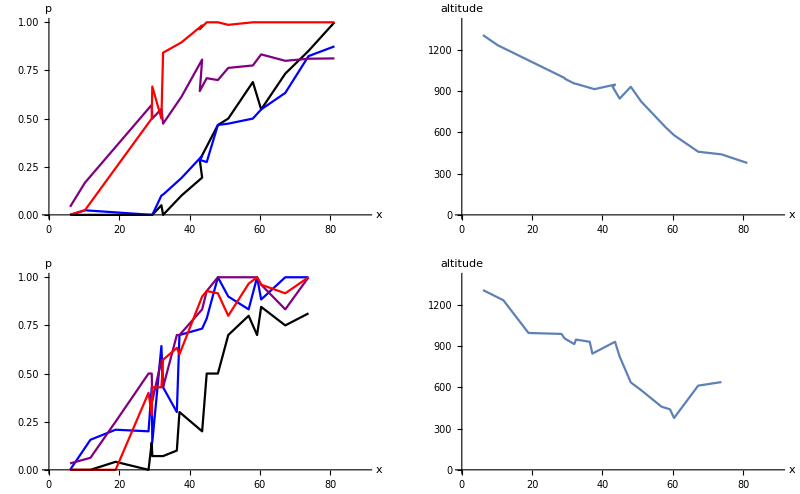

```mathematica
gr[s_]:={Show[MapThread[ListLinePlot[Transpose[{x[s],#1}],PlotStyle->#2,PlotRange->{{0,90},{0,1}}]&,{Transpose[freqs[s]],{Black,Blue,Purple,Red}}],AxesLabel->{"x","p"}],
ListLinePlot[Transpose[{x[s],z[s]}],AxesLabel->{"x","altitude"},PlotRange->{{0,90},{0,1400}}]};GraphicsGrid[{gr[e],gr[m]}]
```

There is no string indication of dominance, apart from purple in erato:

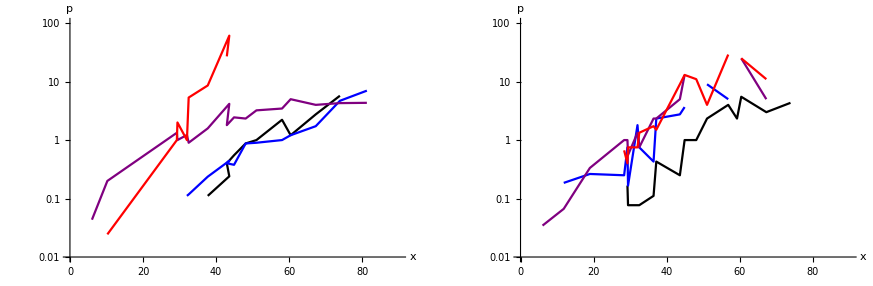

```mathematica
gr2[s_]:=Show[MapThread[ListLogPlot[Transpose[{x[s],#1/(1-#1)}],PlotStyle->#2,Joined->True,PlotRange->{{0,90},{0.01,100}}]&,{Transpose[freqs[s]],{Black,Blue,Purple,Red}}],AxesLabel->{"x","p"}];GraphicsRow[{gr2[e],gr2[m]}]
```

### Fitting clines: erato

#### Fitting a descriptive model

We fit a model of a sigmoid cline, characterised by  {p_0,p_1,w,y}:

p= p_0+(p_1-p_0)/(1+exp[-4(x-y)/w])

We assume binomial sampling, plus underlying allele frequency variation that follows a Beta distribution, with  var(p)=p̂ q̂ F_st.  Thus, the probability of seeing j alleles out of n is:

Beta[αp+j,α q+n-j]/Beta[αp,αq](n
j)  =((α p)_j(α q)_(n-j))/((α)_n)(n
j)  where α=1/F_st-1

Thus, we aim to fit a model with five parameters.

#### WntA: w=34.3, y=54.1, F=0.021

Assuming p_0=0, p_1=1, the MLE is w=34.34, y=54.10, F_st=0.021, giving log(L)=-35.14.

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,1⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,f}],{w,10,1,100},{y,30,10,80},{f,0.1,0.00001,0.9}]
```

{-35.1416,{w→34.3392,y→54.0977,f→0.0214595}}

F is not signiificant

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,1⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,10,1,100},{y,30,10,80}]
```

{-37.0774,{w→34.3601,y→54.2361}}

There is a better fit if p_1=0.835, w=23.55, y=49.09, F_st=0.  However, the gain in log(L) is only 1.69, so this gain is not significant. . The fit is driven by the asymmetric shape of the cline, which gets shallower with increasing x.

```mathematica
fm2=FindMaximum[likCline[dd,{0,p1,w,y,0}],{p1,0.8,0.75,0.95},{w,24,15,35},{y,50,40,60}]
```

{-33.446,{p1→0.834744,w→23.5553,y→49.0943}}

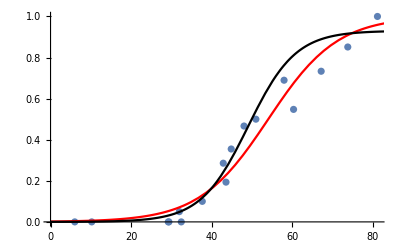

```mathematica
Show[ListPlot[Transpose[{x[e],freqs[e]⟦All,1⟧}]],Plot[{pCline[{0,1,w,y}][x]/.fm⟦2⟧,pCline[{0,0.93,w,y}][x]/.fm2⟦2⟧},{x,0,90},PlotStyle->{Red,Black}]]
```

#### Ro: w=49.1, y=55.7, F=0

Assuming p_0=0, p_1=1, the MLE is w=49.1, y=55.7, F_st=0, giving log(L)= -33.01.

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,2⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,50,40,60},{y,55,40,70}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-33.0108,{w→49.0962,y→55.7128}}

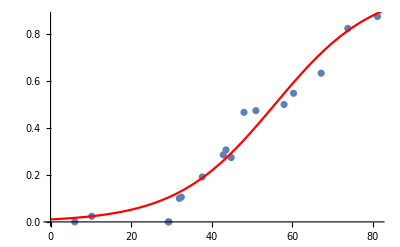

```mathematica
Show[ListPlot[Transpose[{x[e],freqs[e]⟦All,2⟧}]],Plot[pCline[{0,1,w,y}][x]/.fm⟦2⟧,{x,0,90},PlotStyle->Red]]
```

#### Cortex: p_1=0.815, w=38.0, y=30.4, F=0

Assuming p_0=0, p_1=1, the MLE is w=81.3, y=30.4, F_st=0, giving log(L)= -44.87.

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,3⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,70,40,100},{y,30,20,50}]
```

{-44.872,{w→81.3453,y→30.3801}}

There is no significant F:

```mathematica
fm2=FindMaximum[likCline[dd,{0,1,w,y,0.01}],{w,70,40,100},{y,30,20,50}]
```

{-44.1324,{w→78.4677,y→31.5035}}

There is a much better fit if p_1=0.815, w=38.0, y=30.4 giving log(L)=-35.54 (black)

```mathematica
fm2=FindMaximum[likCline[dd,{0,0.815,w,y,0}],{w,80,30,100},{y,30,15,50}]
```

{-35.544,{w→38.0215,y→26.1592}}

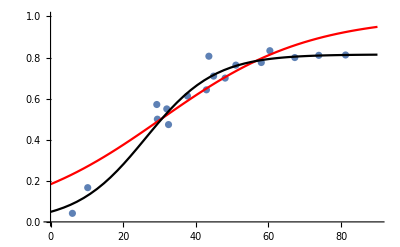

```mathematica
Show[ListPlot[Transpose[{x[e],freqs[e]⟦All,3⟧}],PlotRange->{{0,90},{0,1}}],Plot[{pCline[{0,1,w,y}][x]/.fm⟦2⟧,pCline[{0,0.815,w,y}][x]/.fm2⟦2⟧},{x,0,90},PlotStyle->{Red,Black}]]
```

#### Optix: w=17.0, y=28.2, F=0

Assuming p_0=0, p_1=1, the MLE is w=17.0, y=28.2, F_st=0, giving log(L)= -44.87.

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,4⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,30,10,70},{y,30,20,50}]
```

{-18.8934,{w→16.9569,y→28.2054}}

There is no significant F:

```mathematica
fm2=FindMaximum[likCline[dd,{0,1,w,y,0.001}],{w,30,10,70},{y,30,20,50}]
```

{-19.0142,{w→16.9911,y→28.1772}}

There is no support for p_1<1

```mathematica
fm2=FindMaximum[likCline[dd,{0,0.99,w,y,0}],{w,30,10,70},{y,30,20,50}]
```

{-21.5172,{w→15.8074,y→28.2599}}

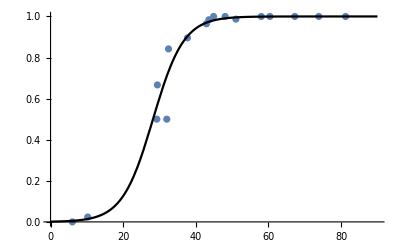

```mathematica
Show[ListPlot[Transpose[{x[e],freqs[e]⟦All,4⟧}],PlotRange->{{0,90},{0,1}}],Plot[pCline[{0,1,w,y}][x]/.fm⟦2⟧,{x,0,90},PlotStyle->{Red,Black}]]
```

#### Comparing all four clines

WntA and Ro are very close. However, Cortex and Optix differ substantially: Cortex is wider and has p_1<1

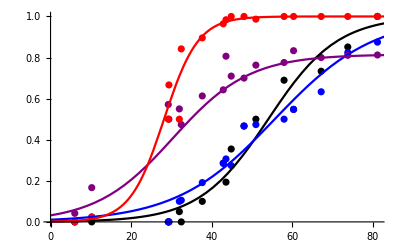

```mathematica
mle[e]={{0,1,34.3,54.1},{0,1,49.1,55.7},{0,0.815,38.0,30.4},{0,1,17.0,28.2}};
Show[
MapThread[ListPlot[Transpose[{x[e],freqs[e]⟦All,#⟧}],PlotStyle->#2]&,{{1,2,3,4},{Black,Blue,Purple,Red}}],MapThread[Plot[pCline[#1][x],{x,0,90},PlotStyle->#2]&,{mle[e],{Black,Blue,Purple,Red}}]]
```

### Fitting clines: melpomene

#### WntA: w=35.7, y=50.6, F=0 p_1=0.85 (ns) w=24.3, y=45.7, F=0

Assuming p_0=0, p_1=1, the MLE is w=34.34, y=54.10, F_st=0.021, giving log(L)=-35.14.

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,1⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,30,15,80},{y,55,30,80}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-32.2613,{w→35.739,y→50.5863}}

F is not significant:

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,1⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0.016}],{w,30,15,80},{y,55,30,80}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-31.7069,{w→35.6901,y→50.2626}}

There is a better fit if p_1=0.850, w=24.28, y=45.65, F_st=0.  However, the gain in log(L) is only 1.69, so this gain is not significant. . The fit is driven by the asymmetric shape of the cline, which gets shallower with increasing x.

```mathematica
fm2=FindMaximum[likCline[dd,{0,p1,w,y,0}],{p1,0.9,0.8,1},{w,30,15,80},{y,55,30,80}]
```

{-27.9708,{p1→0.84947,w→24.2769,y→45.6568}}

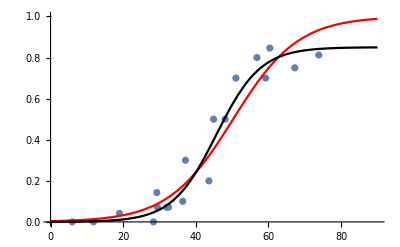

```mathematica
Show[ListPlot[Transpose[{x[m],freqs[m]⟦All,1⟧}]],Plot[{pCline[{0,1,w,y}][x]/.fm⟦2⟧,pCline[{0,0.85,w,y}][x]/.fm2⟦2⟧},{x,0,90},PlotStyle->{Red,Black}],PlotRange->{{0,90},{0,1}}]
```

#### N: w=36.8, y=34.8, F=0.042

Assuming p_0=0, p_1=1, the MLE is w=49.1, y=55.7, F_st=0, giving log(L)= -33.01.

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,2⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,40,20,60},{y,35,20,70}]
```

{-36.7266,{w→38.4741,y→35.2142}}

There is a non-significant improvement in fit if F=0.042

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,2⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,f}],{w,35,20,50},{y,35,20,50},{f,0.04,0.01,0.05}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-35.0926,{w→36.7824,y→34.8188,f→0.0421366}}

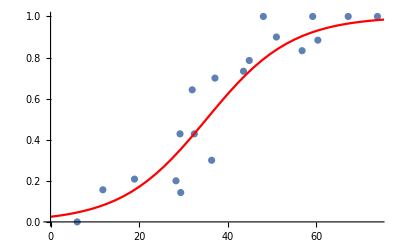

```mathematica
Show[ListPlot[Transpose[{x[m],freqs[m]⟦All,2⟧}]],Plot[pCline[{0,1,w,y}][x]/.fm⟦2⟧,{x,0,90},PlotStyle->Red]]
```

#### Cortex: w=31.3, y=30.3, F=0

Assuming p_0=0, p_1=1, the MLE is w=31.3, y=30.3, F_st=0, giving log(L)= -44.87.

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,3⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,40,30,70},{y,30,20,50}]
```

{-28.8238,{w→31.3155,y→30.3307}}

There is no significant F:

```mathematica
fm2=FindMaximum[likCline[dd,{0,1,w,y,0.002}],{w,40,30,70},{y,30,20,50}]
```

{-28.8047,{w→31.1829,y→30.3111}}

There is a much better fit if p_1=0.815, w=38.0, y=30.4 giving log(L)=-35.54 (black)

```mathematica
fm2=FindMaximum[likCline[dd,{0,0.815,w,y,0}],{w,80,30,100},{y,30,15,50}]
```

{-35.544,{w→38.0215,y→26.1592}}

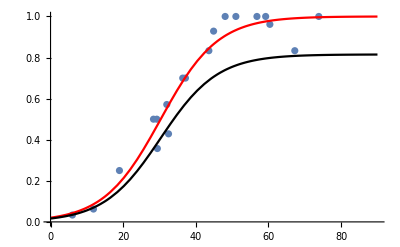

```mathematica
Show[ListPlot[Transpose[{x[m],freqs[m]⟦All,3⟧}],PlotRange->{{0,90},{0,1}}],Plot[{pCline[{0,1,w,y}][x]/.fm⟦2⟧,pCline[{0,0.815,w,y}][x]/.fm2⟦2⟧},{x,0,90},PlotStyle->{Red,Black}]]
```

#### Optix: w=24.5, y=33.6, F=0

Assuming p_0=0, p_1=1, the MLE is w=24.5, y=33.6, F_st=0, giving log(L)= -44.87.

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,4⟧}];
fm=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,30,10,50},{y,30,20,50}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-27.5085,{w→24.4583,y→33.6186}}

There is no significant F:

```mathematica
fm2=FindMaximum[likCline[dd,{0,1,w,y,0.001}],{w,30,10,50},{y,30,20,50}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-27.5562,{w→24.5329,y→33.6286}}

There is no support for p_1<1

```mathematica
fm2=FindMaximum[likCline[dd,{0,0.99,w,y,0}],{w,30,10,70},{y,30,20,50}]
```

{-21.5172,{w→15.8074,y→28.2599}}

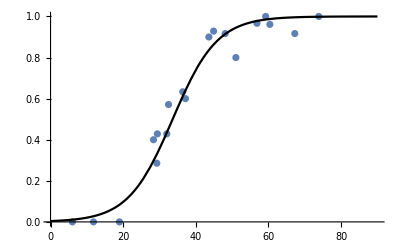

```mathematica
Show[ListPlot[Transpose[{x[m],freqs[m]⟦All,4⟧}],PlotRange->{{0,90},{0,1}}],Plot[pCline[{0,1,w,y}][x]/.fm⟦2⟧,{x,0,90},PlotStyle->{Red,Black}]]
```

#### Comparing all four clines

N, Cortex and Optix (blue, purple, red) are very close. However, WntA (black) is shifted to the right

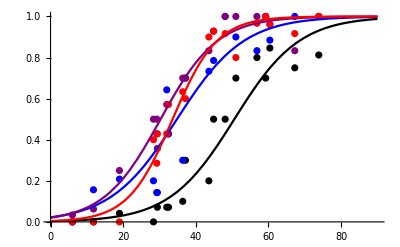

```mathematica
mle[m]={{0,1,35.7,50.6},{0,1,36.8,34.8},{0,1,31.3,30.3},{0,1,24.5,33.6}};
Show[
MapThread[ListPlot[Transpose[{x[m],freqs[m]⟦All,#⟧}],PlotStyle->#2,PlotRange->{{0,90},{0,1}}]&,{{1,2,3,4},{Black,Blue,Purple,Red}}],MapThread[Plot[pCline[#1][x],{x,0,90},PlotStyle->#2]&,{mle[m],{Black,Blue,Purple,Red}}]]
```

### Comparing erato with melpomene

Thick lines: erato, dashed: melpomene; WntA, Ro or N, Cortex, Optix (black, blue, purple, red)

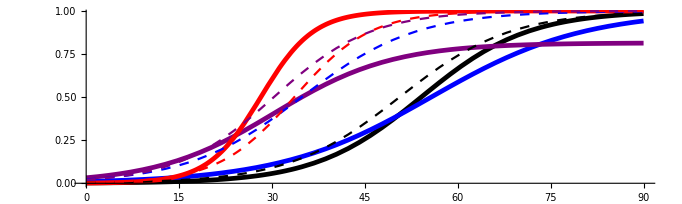

```mathematica
mle[m]={{0,1,35.7,50.6},{0,1,36.8,34.8},{0,1,31.3,30.3},{0,1,24.5,33.6}};
gr[s_,c_]:=MapThread[Plot[pCline[#1][x],{x,0,90},PlotStyle->{#2,c}]&,{mle[s],{Black,Blue,Purple,Red}}];
Show[gr[e,Thickness[0.005]],gr[m,Dashing[{0.01,0.01}]],AspectRatio->0.3]
```

## Fitting clines with dominance

### Modelling a cline at one locus

#### The model: h_1,h_2

The model is that fitnesses multiply across loci, and within loci, fitness is 1-s(P-Q):1+h_1 s(P-Q):1+s(P-Q), where (P - Q) =(p-q)+2pq h_2 assuming HW. Here, the dominance coefficients h_1,h_2 range from -1 to 1. h_1 describes dominance for effects on fitness, whereas h_2 describes dominance for the perceived frequency.

Scaling time to 1/s, distance to σ/√(2s):

∂_t p=∂_(x,x) p+((p-q)+2pq h_2)pq(1-h_1(p-q))=∂_(x,x) p+pqf[p]

In the special case h_1=h_2=0, we have underdominance. If h_1=h_2=1:

∂_t p=∂_(x,x) p+2(1-2 q^2)p q^2

#### The cline cannot be pinned by a compensating selection

We can get an explicit solution for the equilibrium if the solution is static, but with a travelling wave, that is harder. So, we seek a compensating selection coefficient α that prevents movement:

0=∂_(x,x) p+pq(f[p]+s)=∂_x (∂_x p)^2+2pq(f[p]+α)∂_x p
(∂_x p)^2=-∫2pq(f[p]+α)ⅆp    with ∫_0^1 2pq(f[p]+α)ⅆp=0

This requires α=(h_1-2 h_2)/5, and yields:

x=∫ⅆp/(p q √(1+2/5(q-p)(h_2+2 h_1)-4/3 h_1 h_2 pq))

However, this fails: the denominator has a zero at p~0.84.  There is no static solution, because adding a steady negative counter-selection across the whole cline makes the net selection on the right negative, so that there can be an invasion.  In simulations, I used a different method, with an extrinsic selection gradient, which does properly stabilise the cline.   The left plot shows the FD selection, which is positive for q>1/√2, but falls to zero at q=0. Hence, subtracting a countervailing selection will give the only solution as polymorphism on the right, in a balance between that selection and FDS

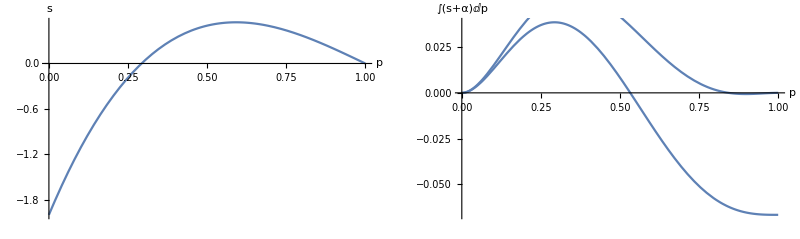

```mathematica
seln[p_,h1_,h2_]:=((2p-1)+2p(1-p)h2)(1-h1(2p-1));
expr=-∫2p(1-p)(seln[p,Subscript[h, 1],Subscript[h, 2]]+α)ⅆp//FullSimplify;GraphicsRow[{Plot[seln[p,1,1],{p,0,1},AxesLabel->{"p","s"}],Show[Plot[expr/.{Subscript[h, 1]->1,Subscript[h, 2]->1,α->0},{p,0,1}],Plot[expr2/.{Subscript[h, 1]->1,Subscript[h, 2]->1,α->-1/5},{p,0,1}],AxesLabel->{"p","∫(s+α)ⅆp"}]}]
```

#### Travelling wave solution

We can instead find the travelling wave solution, which is the same as the solution on a constant countervailing density gradient:

0=∂_(x,x) p+c∂_x p+pq((p-q)+2pq h_2)pq(1-h_1(p-q))

We can reduce this to a first-order ODE by considering  (∂_x p) as a function of p, and setting y=∂_x p=0 when p= 0 and 1

0=y ∂_p y+c y+pq((p-q)+pq h_2)(1-h_1(p-q))

Finding the boundary conditions is tricky.  For small p, seek a solution ⅇ^λx so y~λp, where λ=1/2 (-c+√(4+c^2+4 h_1)). For small q, if h_1=1, we have y~- (2/c)q^2. Otherwise, y~λq, where λ=1/2 (c+√(4+c^2-4 h_1))

This is the solution with complete dominance, h_1=h_2=1:

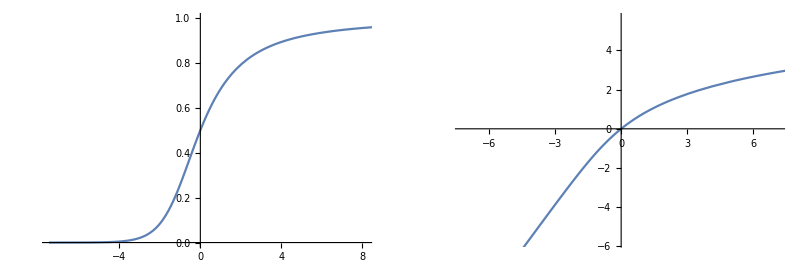

```mathematica
ϵ=10^-4;ss=soln[-0.2244715,1,1,ϵ];
x0=x[1/2]/.ss;
GraphicsRow[{ParametricPlot[{x[p]-x0,p}/.ss,{p,0,1-ϵ},AspectRatio->0.7],ParametricPlot[{x[p]-x0,Log[p/(1-p)]}/.ss,{p,0,1-ϵ},AspectRatio->0.7]}]
```

### Fitting clines with dominance: erato

#### WntA: w=29.92, y=47.30, F=0 Δlog(L)= 4.38 for dominance

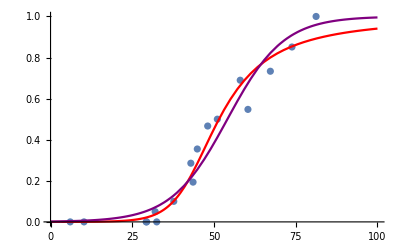

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,1⟧}];
Show[ListPlot[Transpose[{dd⟦All,1⟧,dd⟦All,3⟧/dd⟦All,2⟧}],PlotRange->{{0,100},{0,1}}],Plot[pClineDom[{1,1,29.92,47.30},10^-4][x],{x,0,100},PlotStyle->Red],
Plot[pCline[{0,1,34.34,54.10}][x],{x,0,100},PlotStyle->Purple]]
```

```mathematica
fm=FindMaximum[likClineDom[dd,{1,1,w,y,0}],{w,40,10,80},{y,50,30,70}];
fm2=FindMaximum[likCline[dd,{0,1,w,y,f}],{w,40,10,800},{y,50,30,70},{f,0.01,0,0.1}];
TableForm[{fm,fm2},TableDepth->2]
```

-30.7602 | {w→29.9183,y→47.2957}
-35.1416 | {w→34.3392,y→54.0977,f→0.0214595}

#### Ro: w=47.76, y=55.71, F=0 Δlog(L)= 0.40 for dominance

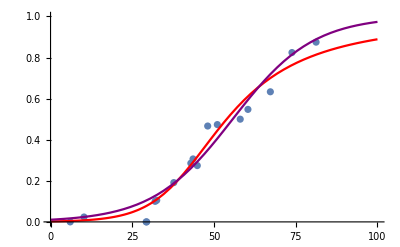

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,2⟧}];
Show[ListPlot[Transpose[{dd⟦All,1⟧,dd⟦All,3⟧/dd⟦All,2⟧}],PlotRange->{{0,100},{0,1}}],Plot[pClineDom[{1,1,47.76,47.13},10^-4][x],{x,0,100},PlotStyle->Red],
Plot[pCline[{0,1,49.10,55.71}][x],{x,0,100},PlotStyle->Purple]]
```

```mathematica
fm=FindMaximum[likClineDom[dd,{1,1,w,y,0}],{w,50,10,80},{y,50,30,70}];
fm2=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,50,10,800},{y,55,30,70}];
TableForm[{fm,fm2},TableDepth->2]
```

-32.6138 | {w→47.7576,y→47.1324}
-33.0108 | {w→49.0962,y→55.7128}

```mathematica
33.01-32.61
```

0.4

#### Cortex: w=38.02, y=26.16, F=0 Δlog(L)= -1.76 against dominance, rel to p_1=0.82; +6.13 rel to {0,1}

```mathematica
fm=FindMaximum[likClineDom[dd,{1,1,w,y,0}],{w,50,10,80},{y,30,10,70}];fm2=FindMaximum[likCline[dd,{0,1,w,y,f}],{w,70,40,100},{y,30,20,80},{f,0.01,0,0.1}];fm3=FindMaximum[likCline[dd,{0,0.815,w,y,0}],{w,80,30,100},{y,30,15,50}];
TableForm[{fm,fm2,fm3},TableDepth->2]
```

-37.2999 | {w→53.8817,y→22.5599}
-44.1321 | {w→78.4459,y→31.5175,f→0.0102476}
-35.544 | {w→38.0215,y→26.1592}

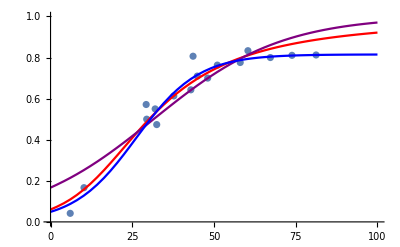

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,3⟧}];
Show[ListPlot[Transpose[{dd⟦All,1⟧,dd⟦All,3⟧/dd⟦All,2⟧}],PlotRange->{{0,100},{0,1}}],Plot[pClineDom[{1,1,53.88,22.56},10^-4][x],{x,0,100},PlotStyle->Red],
Plot[pCline[{0,1,78.45,31.52}][x],{x,0,100},PlotStyle->Purple],
Plot[pCline[{0,0.815,38.02,26.16}][x],{x,0,100},PlotStyle->Blue]]
```

```mathematica
35.54-37.30
```

-1.76

#### Optix: w=16.96, y=28.21, F=0 Δlog(L)= -9.28 against dominance

```mathematica
dd=Transpose[{x[e],2nInds[e],2nInds[e]freqs[e]⟦All,4⟧}];
fm=FindMaximum[likClineDom[dd,{1,1,w,y,f}],{w,15,10,25},{y,20,10,30},{f,0.1,0,0.2}];
fm2=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,20,10,50},{y,30,10,50}];TableForm[{fm,fm2},TableDepth->2]
```

-28.1702 | {w→16.9743,y→20.4392,f→0.128015}
-18.8934 | {w→16.9569,y→28.2054}

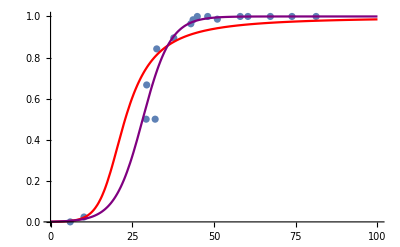

```mathematica
Show[ListPlot[Transpose[{dd⟦All,1⟧,dd⟦All,3⟧/dd⟦All,2⟧}],PlotRange->{{0,100},{0,1}}],Plot[pClineDom[{1,1,16.97,20.44},10^-4][x],{x,0,100},PlotStyle->Red],
Plot[pCline[{0,1,16.96,28.20}][x],{x,0,100},PlotStyle->Purple]]
```

### Fitting clines with dominance: melpomene

#### WntA: w=32.35, y=43.49, F=0 Δlog(L)= 2.28 for dominance

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,1⟧}];
fm=FindMaximum[likClineDom[dd,{1,1,w,y,0}],{w,40,10,80},{y,50,30,70}];
fm2=FindMaximum[likCline[dd,{0,1,w,y,f}],{w,40,10,800},{y,50,30,70},{f,0.01,0,0.1}];
TableForm[{fm,fm2},TableDepth->2]
```

-29.4294 | {w→32.3481,y→43.4932}
-31.7069 | {w→35.6934,y→50.2613,f→0.0161205}

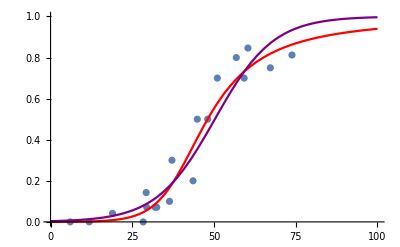

```mathematica
Show[ListPlot[Transpose[{dd⟦All,1⟧,dd⟦All,3⟧/dd⟦All,2⟧}],PlotRange->{{0,100},{0,1}}],Plot[pClineDom[{1,1,w,y}/.fm⟦2⟧,10^-4][x],{x,0,100},PlotStyle->Red],
Plot[pCline[{0,1,w,y}/.fm2⟦2⟧][x],{x,0,100},PlotStyle->Purple]]
```

#### N: w=36.78, y=34.82, F=0 Δlog(L)= -3.09 against dominance

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,2⟧}];
fm=FindMaximum[likClineDom[dd,{1,1,w,y,f}],{w,32,15,45},{y,30,20,40},{f,0.05,0,0.2}];
fm2=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,35,10,50},{y,35,10,50}];
fm3=FindMaximum[likCline[dd,{0,1,w,y,0.042}],{w,35,10,50},{y,35,10,50}];
TableForm[{fm,fm2,fm3},TableDepth->2]
```

-38.1777 | {w→32.1786,y→27.7766,f→0.0793547}
-36.7266 | {w→38.4741,y→35.2142}
-35.0926 | {w→36.783,y→34.8195}

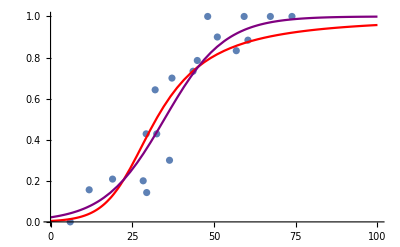

```mathematica
Show[ListPlot[Transpose[{dd⟦All,1⟧,dd⟦All,3⟧/dd⟦All,2⟧}],PlotRange->{{0,100},{0,1}}],Plot[pClineDom[{1,1,w,y}/.fm⟦2⟧,10^-4][x],{x,0,100},PlotStyle->Red],
Plot[pCline[{0,1,w,y}/.fm3⟦2⟧][x],{x,0,100},PlotStyle->Purple]]
```

#### Cortex: w=31.32, y=30.33, F=0 Δlog(L)= -4.56 against dominance

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,3⟧}];
fm=FindMaximum[likClineDom[dd,{1,1,w,y,0}],{w,30,10,50},{y,30,10,50}];fm2=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,30,10,50},{y,30,10,50}];
TableForm[{fm,fm2},TableDepth->2]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-33.3773 | {w→25.8161,y→23.9552}
-28.8238 | {w→31.3155,y→30.3307}

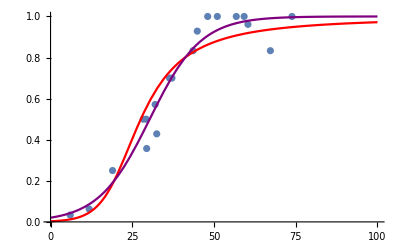

```mathematica
Show[ListPlot[Transpose[{dd⟦All,1⟧,dd⟦All,3⟧/dd⟦All,2⟧}],PlotRange->{{0,100},{0,1}}],Plot[pClineDom[{1,1,w,y}/.fm⟦2⟧,10^-4][x],{x,0,100},PlotStyle->Red],
Plot[pCline[{0,1,w,y}/.fm2⟦2⟧][x],{x,0,100},PlotStyle->Purple]]
```

#### Optix: w=14.91, y=29.81, F=0 Δlog(L)= 4.13 for dominance

```mathematica
dd=Transpose[{x[m],2nInds[m],2nInds[m]freqs[m]⟦All,4⟧}];
fm=FindMaximum[likClineDom[dd,{1,1,w,y,0}],{w,30,10,50},{y,30,10,50}];fm2=FindMaximum[likCline[dd,{0,1,w,y,0}],{w,30,10,50},{y,30,10,50}];
TableForm[{fm,fm2},TableDepth->2]
```

-23.3784 | {w→14.9083,y→29.8067}
-27.5085 | {w→24.4583,y→33.6186}

```mathematica
Show[ListPlot[Transpose[{dd⟦All,1⟧,dd⟦All,3⟧/dd⟦All,2⟧}],PlotRange->{{0,100},{0,1}}],Plot[pClineDom[{1,1,w,y}/.fm⟦2⟧,10^-4][x],{x,0,100},PlotStyle->Red],
Plot[pCline[{0,1,w,y}/.fm2⟦2⟧][x],{x,0,100},PlotStyle->Purple]]
```

-Graphics-

### Summary table

Table 1. Testing for asymmetry of single-locus clines. Linear frequency dependence, with no dominance, maintains a symmetric cline, whereas positive frequency dependence, with full dominance of the lowland alleles, maintains asymmetric clines, with introgression into the lowland population.  The table shows the estimated position and width for each locus, in each species, for the best-fitting model. The last row shows the difference in log likelihood between the best-fitting asymmetric vs symmetric models; a positive value favours asymmetry.  None of the best-fitting models gave evidence for residual variation (i.e., we estimate  F_ST=0).

erato | WntA | Ro | Cortex | Optix | melpomene | WntA | N | Cortex | Optix
width | 29.9 | 47.8 | 38.0 | 17.0 |   | 32.4 | 36.8 | 31.3 | 14.9
position | 47.3 | 55.7 | 26.2 | 28.2 |   | 43.5 | 34.8 | 30.3 | 29.8
dominance | +4.38 | +0.40 | +6.13 | -9.28 |   | +2.28 | -3.09 | -4.56 | +4.13

## Linkage disequilibrium

#### D for each site: erato

This shows the likelihood of D, for Optix & Cortex in the largest site (#7).  D/√(p_1 q_1 p_2 q_2) is only 0.147, and Δlog(L)=1.81, so this is not significant.

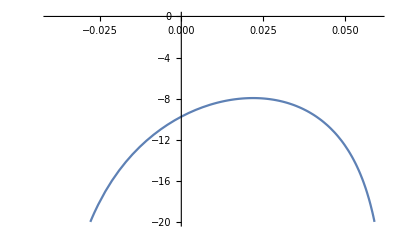

{-9.75388,-7.94513,0.0219619,0.147497}

```mathematica
pp=freqs[e]⟦7,{3,4}⟧;gf=genFreqs[e,{3,4}]⟦7⟧;rd=rangeD[pp];ϵ=10^-4;
Plot[likD[gf,Append[pp,d]],{d,rd⟦1⟧+ϵ,rd⟦2⟧-ϵ},PlotRange->{{-0.04,0.06},{-20,0}}]
Append[mleD[gf],Last[mleD[gf]]/(√(Times@@(pp(1-pp))))]
```

This tabulates D̂ for loci {1,2}.  None are close to significant.

```mathematica
TableForm[Prepend[likDTable[e,{1,2}],{"pop","N","L_(D = 0)","max(L)","D̂"}],TableDepth->2]
```

FindMinimum::reged: The point {0.0449} is at the edge of the search region {-0.0049,0.0449} in coordinate 1 and the computed search direction points outside the region.

pop | N | L_(D = 0) | max(L) | D̂
5 | 10 | -2.0022 | -0.113233 | 0.0449
7 | 115 | -3.08288 | -2.66748 | -0.0130214
8 | 31 | -4.03817 | -4.00543 | 0.00681886
9 | 14 | -2.35414 | -2.28976 | -0.0183223
10 | 31 | -2.00338 | -2.0031 | -0.000805939
11 | 15 | -5.51678 | -4.64913 | -0.0682228
12 | 38 | -4.62028 | -4.39779 | -0.0274955
13 | 29 | -4.99347 | -4.27266 | -0.067097
14 | 21 | -6.56796 | -6.2391 | -0.0364991
15 | 15 | -3.5749 | -3.02394 | -0.049552
16 | 37 | -1.97131 | -1.96869 | 0.0014316

This tabulates D̂ for loci {3,4}.  Only site 7 is close to significant.

```mathematica
TableForm[Prepend[likDTable[e,{3,4}],{"pop","N","L_(D = 0)","max(L)","D̂"}],TableDepth->2]
```

pop | N | L_(D = 0) | max(L) | D̂
2 | 21 | -0.549378 | -0.368843 | -0.00386825
3 | 7 | -2.70092 | -2.03617 | 0.121277
4 | 6 | -5.20538 | -5.20538 | 0.
5 | 10 | -4.42997 | -4.42997 | 0.
6 | 19 | -3.04015 | -1.39087 | -0.0830025
7 | 115 | -9.75388 | -7.94513 | 0.0219619
8 | 31 | -0.473297 | -0.262448 | -0.00302175
9 | 14 | -1.5589 | -1.10964 | -0.0126551
12 | 38 | -0.570059 | -0.305337 | -0.00301634

#### D for each site: melpomene

This tabulates D̂ for loci {1,2}.  None are close to significant.

```mathematica
TableForm[Prepend[likDTable[m,{1,2}],{"pop","N","L_(D = 0)","max(L)","D̂"}],TableDepth->2]
```

pop | N | L_(D = 0) | max(L) | D̂
3 | 12 | -0.764426 | -0.527554 | -0.00858056
5 | 7 | -0.817925 | -0.268825 | -0.0611245
6 | 7 | -0.574749 | -0.415721 | -0.0101041
7 | 7 | -1.01522 | -0.553653 | 0.0254102
8 | 7 | -2.73696 | -2.53154 | 0.0407163
9 | 15 | -0.710234 | -0.264336 | -0.0299
10 | 5 | -2.7838 | -2.14922 | 0.0899
11 | 15 | -1.22226 | -0.488438 | 0.0532333
12 | 7 | -2.49376 | -2.49376 | 0.
14 | 5 | -3.22183 | -1.88154 | 0.0699
15 | 15 | -3.76341 | -3.76341 | 0.
17 | 13 | -3.05875 | -2.71178 | 0.0207101

This tabulates D̂ for loci {1,3}.  None is close to significant.

```mathematica
TableForm[Prepend[likDTable[m,{1,3}],{"pop","N","L_(D = 0)","max(L)","D̂"}],TableDepth->2]
```

pop | N | L_(D = 0) | max(L) | D̂
3 | 12 | -0.664087 | -0.37163 | -0.0103167
5 | 7 | -1.13117 | -0.271477 | 0.0713286
6 | 7 | -2.40152 | -1.93995 | -0.0254102
7 | 7 | -3.00754 | -2.10985 | -0.0407163
8 | 7 | -1.62124 | -1.03435 | -0.0305122
9 | 15 | -2.98858 | -2.97991 | -0.00333333
10 | 5 | -1.39751 | -1.24203 | -0.0807107
11 | 15 | -4.37379 | -4.37379 | 0.
12 | 7 | -1.07144 | -1.07144 | 0.
17 | 13 | -1.13855 | -0.970498 | -0.00581716
18 | 6 | -6.25623 | -5.89853 | 0.0416667

This tabulates D̂ for loci {2,3}.  None is close to significant.

```mathematica
TableForm[Prepend[likDTable[m,{2,3}],{"pop","N","L_(D = 0)","max(L)","D̂"}],TableDepth->2]
```

pop | N | L_(D = 0) | max(L) | D̂
2 | 16 | -1.23092 | -0.8822 | -0.00966563
3 | 12 | -3.24375 | -3.20006 | -0.0104167
4 | 5 | -4.58145 | -2.94349 | 0.0999
5 | 7 | -4.08721 | -3.42246 | 0.121277
6 | 7 | -2.46124 | -2.36112 | 0.0204082
7 | 7 | -2.98449 | -0.539822 | -0.152961
8 | 7 | -4.63701 | -4.63268 | -0.0072663
9 | 15 | -5.91862 | -5.72684 | 0.0233333
10 | 5 | -1.39751 | -1.24203 | 0.0807107
11 | 15 | -6.75917 | -5.76313 | 0.0500215
12 | 7 | -3.9161 | -2.91748 | 0.0560224
17 | 13 | -0.490848 | -0.368272 | -0.00433787

#### Plots of log(L) vs x for all pairs

erato: the top row is for clines that coincide (WntA,Ro) and (Cortex, Optix). Other rows are between loci that are staggered.  All the estimates fluctuate around zero:

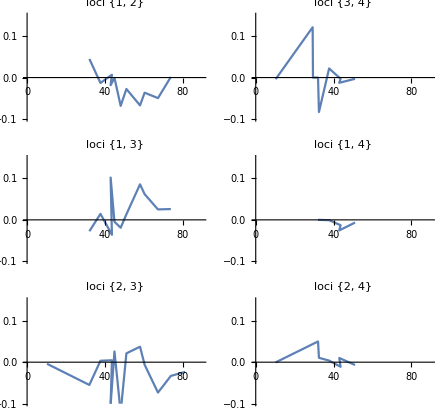

```mathematica
gr[s_,loci_]:=Module[{tt=likDTable[s,loci]},
ListLinePlot[Transpose[{x[s]⟦tt⟦All,1⟧⟧,tt⟦All,5⟧}],PlotRange->{{0,90},{-0.1,0.15}},AxesOrigin->{0,0},PlotLabel->"loci "<>ToString[loci]]];
GraphicsGrid[{{gr[e,{1,2}],gr[e,{3,4}]},
{gr[e,{1,3}],gr[e,{1,4}]},
{gr[e,{2,3}],gr[e,{2,4}]}}]
```

melpomene: the top row is for clines that coincide (N, Cortex, Optix):

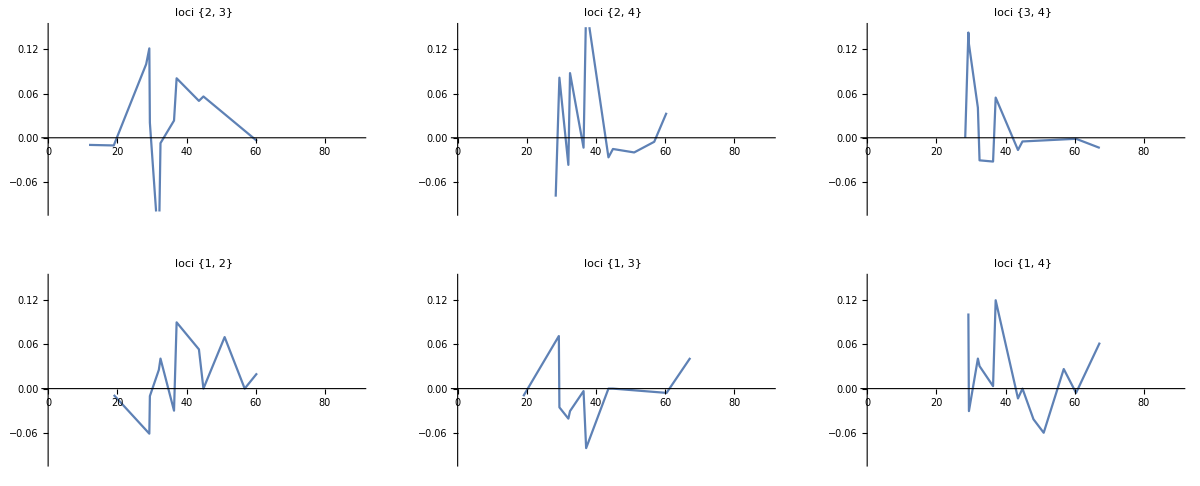

```mathematica
GraphicsGrid[{{gr[m,{2,3}],gr[m,{2,4}],gr[m,{3,4}]},
{gr[m,{1,2}],gr[m,{1,3}],gr[m,{1,4}]}}]
```

#### Estimates of R=D/(√(p_1 q_1 p_2 q_2)) for all pairs

In order to make some overall estimate of LD, we need a measure that to some degree corrects across varying allele frequencies.  No measure is ideal, but I use the correlation R.

Although the estimates are more positive than  not,  none are near significance (compare log(L) for R=0 vs the MLE, L̂). In bold, are indicated loci whose clines coincide.  erato is followed by melpomene:

```mathematica
TableForm[Prepend[likRTable[e],{"loci","L_(R = 0)","L̂","R̂"}],TableDepth->2]
```

loci | L_(R=0) | L̂ | R̂
{WntA,Ro} | -40.7255 | -40.4365 | -0.013384
{WntA,Cortex} | -37.565 | -36.9393 | 0.0413259
{WntA,Optix} | -10.2629 | -10.0467 | -0.012729
{Ro,Cortex} | -46.1284 | -45.8348 | -0.00975521
{Ro,Optix} | -7.64323 | -7.57094 | 0.0102422
{Cortex,Optix} | -28.2819 | -28.1783 | 0.0227139

```mathematica
TableForm[Prepend[likRTable[m],{"loci","L_(R = 0)","L̂","R̂"}],TableDepth->2]
```

loci | L_(R=0) | L̂ | R̂
{WntA,N} | -23.1633 | -22.8775 | 0.0467952
{WntA,Cortex} | -26.0517 | -25.906 | -0.0143726
{WntA,Optix} | -29.0702 | -28.9937 | 0.0297197
{N,Cortex} | -41.7083 | -41.3131 | 0.0771787
{N,Optix} | -26.3673 | -26.2531 | 0.0486623
{Cortex,Optix} | -34.2736 | -34.2652 | -0.00533928

#### Overall estimates

These are the estimated R, using all populations:

species |   |   | R̂ | ΔL | limits |  
erato | coincident | 2 pairs | -0.025 | 0.21 | -0.099 | 0.054
  | staggered | 4 pairs | -0.016 | 0.16 | -0.075 | 0.040
melpomene | coincident | 3 pairs | 0.042 | 0.28 | -0.068 | 0.154
  | staggered | 3 pairs | 0.007 | 0.01 | -0.083 | 0.098

We can instead only use the populations which are highly polymorphic (h=√(p_1 q_1 p_2 q_2)>0.1) -  this differs between locus pairs.  Estimates in melpomene are then somewhat higher, but still far from significant. Changing to a threshold h>0.2 does not help.

species |   |   | R̂ | ΔL | limits |  
erato | coincident | 2 pairs | -0.012 | 0.04 | -0.093 | 0.074
  | staggered | 4 pairs | 0.003 | 0.01 | -0.061 | 0.066
melpomene | coincident | 3 pairs | 0.064 | 0.54 | -0.058 | 0.184
  | staggered | 3 pairs | 0.026 | 0.14 | -0.071 | 0.116

#### Comparison with Mallet et al 1990

These are the sample sizes for the pairs of loci at coincident clines, with sites having h>0.1.  For comparison, in Mallet et al (1990) there were 650 individuals in sites 0.1<p<0.9, and 3 pairs of loci.  The value of R=0.35  in erato is much higher than the upper limits of 0.074 seen here.  Interpretation of the 4 melpomene genes in Mallet et al. is harder, because of linkage, but the associations amongst unlinked genes were higher than in erato (0.4-0.6 say).  Again, this is higher than the upper limit seen here.

In theory, the gametic correlations are expected to peak in the center of the hybrid zone (BARTON1982; MALLETand BARTON1989a), but the pattern is not noticeable from the data, presumably because of the small sample sizes, and possibly also because disequilibria might vary between sites with local differences in migration or selection. Thus, we can get only a crude idea of the peak correlation. If we exclude the two sites with p outside the range 0.1-0.9 (km 40-41 Tarapoto-Yurimaguas and Davidcillo) the average R is about 0.27; however, the peak may be much higher, as much as 0.45-0.48; we will take 0.35 as a sensible value. Comparing this value with the appropriate set of results in Figure 5B of MALLETand BARTON (1989a), w e find that this peak disequilibrium corresponds to a selection pressure of s = 0.23 per locus. We use Figure 2C of MALLETand BARTON(1989a) to infer that this level of selection implies a standardized maximum slope, a / w , of 0.27. T h e observed average width is about 9.59 km. Thus u = 0.27 X 9.59 = 2.6 km.

```mathematica
{Total[nInds[e]⟦pickPol[e,0.1,#]⟧]&/@{{1,2},{3,4}},Total[nInds[m]⟦pickPol[m,0.1,#]⟧]&/@{{2,3},{2,4},{3,4}}}
```

{{346,157},{87,80,74}}

#### Working for sites with h>0.2

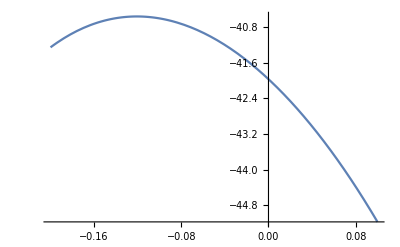

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-40.5608,{r→-0.12075}},1.40634,0.023767,0.023767}

```mathematica
ff=Total[Flatten[likRset[e,0.2,#]&/@{{1,2},{3,4}}]];
Plot[ff,{r,-0.2,0.1}]
fm=FindMaximum[ff,{r,0,-0.2,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

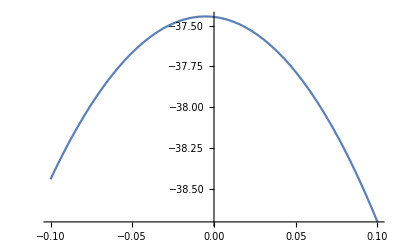

{{-37.4441,{r→-0.00525328}},0.00304136,-0.138738,0.126544}

```mathematica
ff=Total[Flatten[likRset[e,0.2,#]&/@{{1,3},{1,4},{2,3},{2,4}}]];
Plot[ff,{r,-0.1,0.1}]
fm=FindMaximum[ff,{r,0,-0.1,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

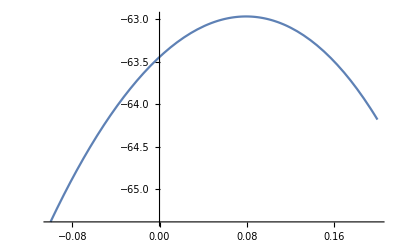

{{-62.9685,{r→0.0794181}},0.475869,-0.0840131,0.232156}

```mathematica
ff=Total[Flatten[likRset[m,0.2,#]&/@{{2,3},{2,4},{3,4}}]];
Plot[ff,{r,-0.1,0.2}]
fm=FindMaximum[ff,{r,0,-0.1,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

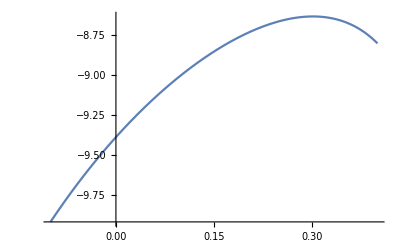

{{-8.63239,{r→0.301351}},0.754806,-0.1999,-0.1999}

```mathematica
ff=Total[Flatten[likRset[m,0.2,#]&/@{{1,2},{1,3},{1,4}}]];
Plot[ff,{r,-0.1,0.4}]
fm=FindMaximum[ff,{r,0,-0.1,0.4}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

#### Working for sites with h>0.1

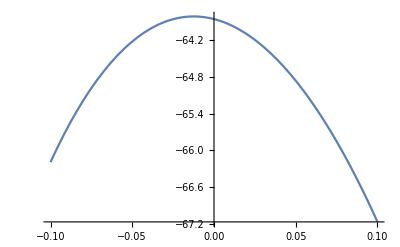

{{-63.8108,{r→-0.0124222}},0.0427597,-0.0931368,0.0740784}

```mathematica
ff=Total[Flatten[likRset[e,0.1,#]&/@{{1,2},{3,4}}]];
Plot[ff,{r,-0.1,0.1}]
fm=FindMaximum[ff,{r,0,-0.1,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

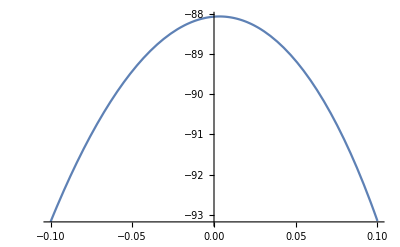

{{-88.0707,{r→0.00333656}},0.00540568,-0.0614633,0.0656935}

```mathematica
ff=Total[Flatten[likRset[e,0.1,#]&/@{{1,3},{1,4},{2,3},{2,4}}]];
Plot[ff,{r,-0.1,0.1}]
fm=FindMaximum[ff,{r,0,-0.1,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

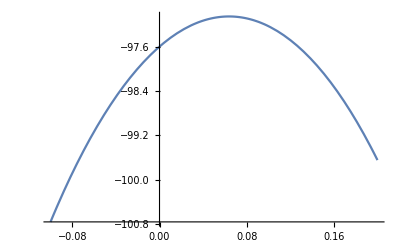

{{-97.0548,{r→0.0638158}},0.543104,-0.0577817,0.183999}

```mathematica
ff=Total[Flatten[likRset[m,0.1,#]&/@{{2,3},{2,4},{3,4}}]];
Plot[ff,{r,-0.1,0.2}]
fm=FindMaximum[ff,{r,0,-0.1,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

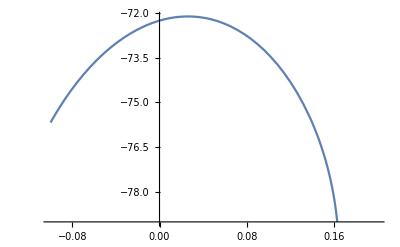

{{-72.1195,{r→0.0260516}},0.139502,-0.0709769,0.11639}

```mathematica
ff=Total[Flatten[likRset[m,0.1,#]&/@{{1,2},{1,3},{1,4}}]];
Plot[ff,{r,-0.1,0.2}]
fm=FindMaximum[ff,{r,0,-0.1,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

#### Working for estimates using all populations

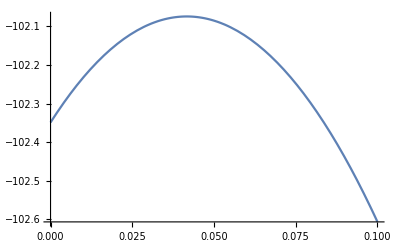

{{-102.074,{r→0.0416701}},0.275176,-0.0684029,0.15397}

```mathematica
ff=Total[Flatten[Outer[likR[m,#1,#2][r]&,Range[nPops[m]],{{2,3},{2,4},{3,4}},1]/.Indeterminate->0]];
Plot[ff,{r,0,0.1}]
fm=FindMaximum[ff,{r,0.04}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,0}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

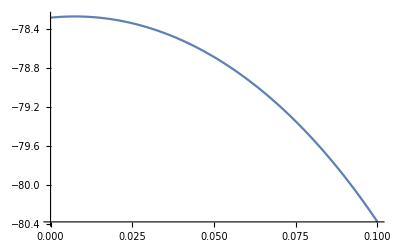

{{-78.2726,{r→0.00747083}},0.0126218,-0.0831428,0.0977441}

```mathematica
ff=Total[Flatten[Outer[likR[m,#1,#2][r]&,Range[nPops[m]],{{1,2},{1,3},{1,4}},1]/.Indeterminate->0]];
Plot[ff,{r,0,0.1}]
fm=FindMaximum[ff,{r,0.01,-0.1,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

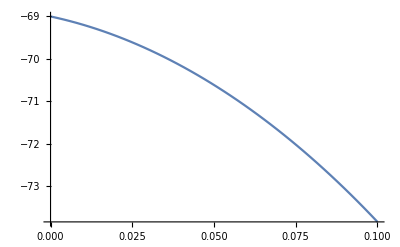

{{-68.7982,{r→-0.0252109}},0.20925,-0.0986608,0.0536182}

```mathematica
ff=Total[Flatten[Outer[likR[e,#1,#2][r]&,Range[nPops[e]],{{1,2},{3,4}},1]/.Indeterminate->0]];
Plot[ff,{r,0,0.1}]
fm=FindMaximum[ff,{r,0.01,-0.15,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

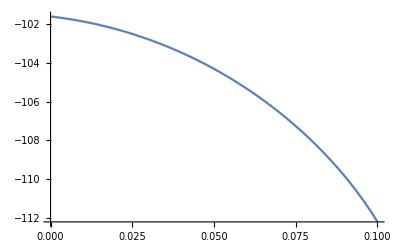

{{-101.443,{r→-0.0160067}},0.156272,-0.0745584,0.039713}

```mathematica
ff=Total[Flatten[Outer[likR[e,#1,#2][r]&,Range[nPops[e]],{{1,3},{1,4},{2,3},{2,4}},1]/.Indeterminate->0]];
Plot[ff,{r,0,0.1}]
fm=FindMaximum[ff,{r,0.01,-0.15,0.1}];
{fm,(fm⟦1⟧-ff/.r->0),r/.FindRoot[ff==fm⟦1⟧-2,{r,-0.05}],r/.FindRoot[ff==fm⟦1⟧-2,{r,0.1}]}
```

### Naive approach: marginal significance in melpomene, none in erato

To give an independent check, we can ask about the variance of a “hybrid index”. I consider loci {2,3,4} in melpomene, using populations with h>0.15 for at least one pair of loci.  The total sample is then 80 individuals from 9 samples:

```mathematica
pops=Union@@(pickPol[m,0.15,#]&/@{{2,3},{2,4},{3,4}});
{Length[pops],Total[nInds[m]⟦pops⟧]}
```

{9,80}

```mathematica
TableForm[Transpose[{pops,nInds[m]⟦pops⟧,x[m]⟦pops⟧}]]
```

3 | 12 | 18.97
4 | 5 | 28.34
5 | 7 | 29.25
6 | 7 | 29.41
7 | 7 | 32.
8 | 7 | 32.48
9 | 15 | 36.39
10 | 5 | 37.14
11 | 15 | 43.59

```mathematica
shuffle[g_List]:=Transpose[RandomSample/@Transpose[g]];
```

I calculate a “hybrid index” for N, Cortex, Optix in melpomene, and find its mean variance across the 9 sites with h>0.15.  I then compare this with 10^4 replicate shuffles, shuffling genotypes within each population. Only 4.2% of shuffled populations have variance higher than observed (1.77 s.d.)

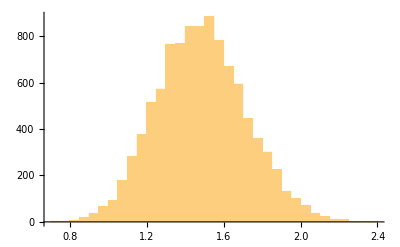

{1.88901,1.48347,0.229346,1.76822,424}

```mathematica
nreps=10^4;
obs=gen[m]⟦pops,All,{2,3,4}⟧;
reps=Table[shuffle/@obs,{nreps}];
vl=N[Variance[Total/@Map[Total,#,{2}]]]&/@obs;
vlS=Table[N[Variance[Total/@Map[Total,#,{2}]]]&/@reps⟦j⟧,{j,nreps}];
vd=Sort[Mean/@vlS];
Histogram[vd]
mn=Mean[Mean/@vlS];mnObs=Mean[vl];sd=StandardDeviation[Mean/@vlS];{mnObs,mn,sd,(mnObs-mn)/sd,Length[Select[vd,#>Mean[vl]&]]}
```

The same, for {WntA,Ro} in erato: the variance in HI  is lower than the shuffled mean

```mathematica
pops=Union@@(pickPol[e,0.15,#]&/@{{1,2}});
{Length[pops],Total[nInds[e]⟦pops⟧]}
```

{8,194}

```mathematica
nreps=10^4;
obs=gen[e]⟦pops,All,{1,2}⟧;
reps=Table[shuffle/@obs,{nreps}];
vl=N[Variance[Total/@Map[Total,#,{2}]]]&/@obs;
vlS=Table[N[Variance[Total/@Map[Total,#,{2}]]]&/@reps⟦j⟧,{j,nreps}];
vd=Sort[Mean/@vlS];
```

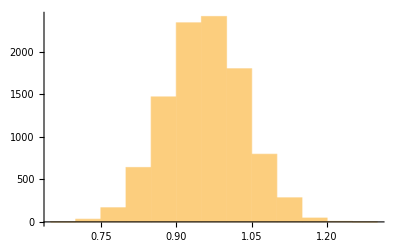

{0.803604,0.957277,0.0773386,-1.98702,9774}

```mathematica
Histogram[vd]
mn=Mean[Mean/@vlS];mnObs=Mean[vl];sd=StandardDeviation[Mean/@vlS];{mnObs,mn,sd,(mnObs-mn)/sd,Length[Select[vd,#>Mean[vl]&]]}
```

The same, for {Cortex, Optix} in erato: the variance in HI  is lower than the shuffled mean. I use h>0.1; also, no significance

```mathematica
pops=Union@@(pickPol[e,0.1,#]&/@{{3,4}});
{Length[pops],Total[nInds[e]⟦pops⟧]}
```

{5,157}

```mathematica
nreps=10^4;
obs=gen[e]⟦pops,All,{3,4}⟧;
reps=Table[shuffle/@obs,{nreps}];
vl=N[Variance[Total/@Map[Total,#,{2}]]]&/@obs;
vlS=Table[N[Variance[Total/@Map[Total,#,{2}]]]&/@reps⟦j⟧,{j,nreps}];
vd=Sort[Mean/@vlS];
```

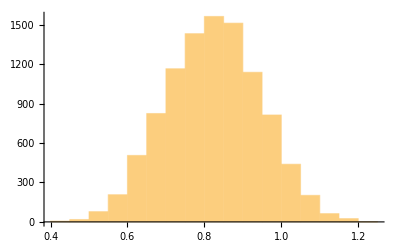

{0.887107,0.823435,0.121426,0.524373,3088}

```mathematica
Histogram[vd]
mn=Mean[Mean/@vlS];mnObs=Mean[vl];sd=StandardDeviation[Mean/@vlS];{mnObs,mn,sd,(mnObs-mn)/sd,Length[Select[vd,#>Mean[vl]&]]}
```

## LD on phenotypes

#### Checking erato data: ~5% error rate

These checks suggest a modest error rate - and actually, it is not obvious taht these are “errors”, since the SNP may not be completely associated with the causal alleles. Presumably, there is evidence from crosses on this.

This makes a table with the position of each genotypes individual in the phenotype data:

```mathematica
ct=Table[Position[codesP[e],#]&/@codes[e]⟦j⟧,{j,nPops[e]}]
```

{{{{35,1}},{{35,2}},{{35,3}},{{35,4}},{{35,5}},{{35,6}},{{35,7}},{{35,8}},{{35,9}},{{35,10}},{{35,11}},{{35,12}}},{{{34,1}},{{34,2}},{{34,3}},{{34,4}},{{34,5}},{{34,6}},{{34,7}},{{34,8}},{{34,9}},{{34,10}},{{34,11}},{{34,12}},{{34,13}},{{34,14}},{{34,15}},{{34,16}},{{34,17}},{{34,18}},{{34,19}},{{34,20}},{{33,1}}},{{{30,1}},{{30,2}},{{30,3}},{{30,4}},{{30,5}},{{30,6}},{{30,7}}},{{{26,1}},{{26,2}},{{26,3}},{{26,4}},{{26,5}},{{26,6}}},{{{22,1}},{{22,2}},{{22,3}},{{22,4}},{{22,5}},{{22,6}},{{22,7}},{{22,8}},{{22,9}},{{22,10}}},{{{27,1}},{{27,2}},{{27,3}},{{27,4}},{{27,5}},{{27,6}},{{27,7}},{{27,8}},{{27,9}},{{27,10}},{{27,11}},{{27,12}},{{27,13}},{{27,14}},{{27,15}},{{27,16}},{{27,17}},{{27,18}},{{27,19}}},{{{24,9}},{{24,45}},{{24,1}},{{24,2}},{{24,3}},{{24,4}},{{24,5}},{{24,6}},{{24,7}},{{24,8}},{{24,10}},{{24,11}},{{24,12}},{{24,13}},{{24,14}},{{24,15}},{{24,16}},{{24,17}},{{24,18}},{{24,19}},{{24,20}},{{24,21}},{{24,22}},{{24,23}},{{24,24}},{{24,25}},{{24,26}},{{24,27}},{{24,28}},{{24,29}},{{24,30}},{{24,31}},{{24,32}},{{24,33}},{{24,34}},{{24,35}},{{24,36}},{{24,37}},{{24,38}},{{24,39}},{{24,40}},{{24,41}},{{24,42}},{{24,43}},{{24,44}},{{24,46}},{{24,47}},{{24,48}},{{24,49}},{{24,50}},{{24,51}},{{24,52}},{{24,53}},{{24,54}},{{24,55}},{{24,56}},{{24,57}},{{20,1}},{{20,2}},{{20,3}},{{20,4}},{{20,5}},{{20,6}},{{20,7}},{{20,8}},{{20,9}},{{20,10}},{{20,11}},{{20,12}},{{20,13}},{{20,14}},{{20,15}},{{20,16}},{{20,17}},{{20,18}},{{20,19}},{{20,20}},{{20,21}},{{20,22}},{{20,23}},{{20,24}},{{20,25}},{{20,26}},{{20,27}},{{20,28}},{{20,29}},{{20,30}},{{20,31}},{{20,32}},{{20,33}},{{20,34}},{{20,35}},{{20,36}},{{20,37}},{{20,38}},{{20,39}},{{20,40}},{{20,41}},{{20,42}},{{20,43}},{{20,44}},{{20,45}},{{20,46}},{{20,47}},{{20,48}},{{20,49}},{{20,50}},{{20,51}},{{20,52}},{{20,53}},{{20,54}},{{20,55}},{{20,56}},{{20,57}},{{20,58}}},{{{16,18}},{{16,1}},{{16,2}},{{16,3}},{{16,4}},{{16,5}},{{16,6}},{{16,7}},{{16,8}},{{16,9}},{{16,10}},{{16,11}},{{16,12}},{{16,13}},{{16,14}},{{16,15}},{{16,16}},{{16,17}},{{16,19}},{{16,20}},{{16,21}},{{16,22}},{{16,23}},{{16,24}},{{16,25}},{{16,26}},{{16,27}},{{16,28}},{{16,29}},{{16,30}},{{16,31}}},{{{14,1}},{{14,2}},{{14,3}},{{10,1}},{{10,2}},{{10,3}},{{10,4}},{{10,5}},{{10,6}},{{10,7}},{{10,8}},{{10,9}},{{10,10}},{{10,11}}},{{{18,1}},{{18,2}},{{18,3}},{{18,4}},{{18,5}},{{18,6}},{{18,7}},{{18,8}},{{18,9}},{{18,10}},{{18,11}},{{18,12}},{{18,13}},{{18,14}},{{18,15}},{{18,16}},{{18,17}},{{18,18}},{{18,19}},{{18,20}},{{18,21}},{{18,22}},{{18,23}},{{18,24}},{{18,25}},{{18,26}},{{18,27}},{{18,28}},{{18,29}},{{18,30}},{{18,31}}},{{{11,1}},{{11,2}},{{11,3}},{{11,4}},{{11,5}},{{11,6}},{{11,7}},{{11,8}},{{11,9}},{{11,10}},{{11,11}},{{11,12}},{{11,13}},{{11,14}},{{11,15}}},{{{13,1}},{{13,2}},{{13,3}},{{13,4}},{{13,5}},{{13,6}},{{13,7}},{{13,8}},{{13,9}},{{13,10}},{{13,11}},{{13,12}},{{13,13}},{{13,14}},{{13,15}},{{13,16}},{{13,17}},{{13,18}},{{13,19}},{{13,20}},{{13,21}},{{13,22}},{{13,23}},{{13,24}},{{13,25}},{{13,26}},{{13,27}},{{13,28}},{{13,29}},{{13,30}},{{13,31}},{{13,32}},{{13,33}},{},{},{},{},{}},{{{8,1}},{{8,2}},{{8,3}},{{8,4}},{{8,5}},{{8,6}},{{8,7}},{{8,8}},{{8,9}},{{8,10}},{{8,11}},{{8,12}},{{8,13}},{{8,14}},{{8,15}},{{8,16}},{{8,17}},{{8,18}},{{8,19}},{{8,20}},{{8,21}},{{8,22}},{{8,23}},{{4,1}},{{4,2}},{{4,3}},{{4,4}},{{4,5}},{{4,6}}},{{{7,1}},{{7,2}},{{7,3}},{{7,4}},{{7,5}},{{7,6}},{{7,7}},{{7,8}},{{7,9}},{{7,10}},{{7,11}},{{7,12}},{{7,13}},{{7,14}},{{7,15}},{{7,16}},{{7,17}},{{7,18}},{{7,19}},{{7,20}},{{7,21}}},{{{5,1}},{{5,2}},{{5,3}},{{5,4}},{{5,5}},{{5,6}},{{5,7}},{{5,8}},{{5,9}},{{5,10}},{{5,11}},{{5,12}},{{5,13}},{{5,14}},{{5,15}}},{{{3,1}},{{3,2}},{{3,3}},{{3,4}},{{3,5}},{{3,7}},{{3,10}},{{3,12}},{{3,13}},{{3,14}},{{3,16}},{{3,17}},{{3,19}},{{3,25}},{{3,26}},{{3,27}},{{3,28}},{{3,29}},{{3,30}},{{3,31}},{{3,33}},{{3,34}},{{3,35}},{{3,37}},{{3,6}},{{3,8}},{{3,9}},{{3,11}},{{3,15}},{{3,18}},{{3,20}},{{3,21}},{{3,22}},{{3,23}},{{3,24}},{{3,32}},{{3,36}}},{{{1,1}},{{1,2}},{{1,3}},{{1,4}},{{2,1}},{{2,2}},{{2,3}},{{2,4}}}}

This checks that every genotypes individual appears once.  5 individuals in population #12 are missing from the phenotype data.

```mathematica
dt=Table[Union[Dimensions/@ct⟦j⟧],{j,nPops[e]}]
```

{{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{0},{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{{1,2}}}

Some of the genotyped samples appear in two different locations in the phenotype data - presumably nearby:

```mathematica
pt=Table[Union[DeleteCases[ct⟦j⟧,{}]⟦All,1,1⟧],{j,nPops[e]}]
```

{{35},{33,34},{30},{26},{22},{27},{20,24},{16},{10,14},{18},{11},{13},{4,8},{7},{5},{3},{1,2}}

This lists {phenotype,genotype} for each of the individuals & loci:

```mathematica
pgList[j_]:=Module[{pList,gList},
pList=Extract[phen[e],#]&/@Flatten[ct⟦j⟧,1];
gList=Map[Total,gen[e]⟦j,All,{1,2,4}⟧,{2}];
MapThread[Transpose[{#1,#2}]&,{gList,PadRight[pList,Length[gList],{{∅,∅,∅}}]}]];
pgList[All]:=Flatten[pgList/@Range[nPops[e]],1];
```

This shows, for the whole dataset, how genotype corresponds to phenotype.

```mathematica
TableForm[Sort[Tally[#]]&/@Transpose[pgList[All]],TableDepth->2]
```

{{0,0},214} | {{0,1},10} | {{0,2},2} | {{0,∅},4} | {{1,0},2} | {{1,1},102} | {{1,2},11} | {{1,∅},1} | {{2,1},4} | {{2,2},79}
{{0,0},215} | {{1,0},129} | {{1,1},6} | {{1,∅},2} | {{2,0},11} | {{2,1},63} | {{2,∅},3} |  |  | 
{{0,0},33} | {{0,1},5} | {{1,0},1} | {{1,1},40} | {{1,2},2} | {{2,1},6} | {{2,2},337} | {{2,∅},5} |  |

This organises a table for each locus:

```mathematica
gpt[j_]:=Module[{aa},
aa=Sort[Tally[Transpose[pgList[All]]⟦j⟧]];
aa=DeleteCases[aa,{{_,∅},_}];
GatherBy[aa,#⟦1,1⟧&]];
```

The SNP genotype is indicated by the first integer (0,1,2), and the inferred phenotype by the second; for WntA, 6.8% error

```mathematica
TableForm[gpt[1],TableDepth->2]
```

{{0,0},214} | {{0,1},10} | {{0,2},2}
{{1,0},2} | {{1,1},102} | {{1,2},11}
{{2,1},4} | {{2,2},79} |

For Ro,  4% error (the + allele here is recessive)

```mathematica
TableForm[gpt[2],TableDepth->2]
```

{{0,0},215} | 
{{1,0},129} | {{1,1},6}
{{2,0},11} | {{2,1},63}

For Optix,  3.3% error

```mathematica
TableForm[gpt[3],TableDepth->2]
```

{{0,0},33} | {{0,1},5} | 
{{1,0},1} | {{1,1},40} | {{1,2},2}
{{2,1},6} | {{2,2},337} |

### Naive approach TO DO

To give an independent check, we can ask about the variance of a “hybrid index”. I consider loci {WntA, Ro} in erato, using populations with h>0.1 for at least one pair of loci.  The total sample is then 156 individuals from 10 samples:

```mathematica
pops=Union@@(pickPol[e,0.1,#]&/@{{1,2}});
{Length[pops],Total[nInds[e]⟦pops⟧]}
```

{10,156}

```mathematica
TableForm[Transpose[{pops,nInds[e]⟦pops⟧,x[e]⟦pops⟧}]]
```

7 | 21 | 37.7
8 | 23 | 43.59
9 | 7 | 42.915
10 | 11 | 44.89
11 | 15 | 48.07
12 | 6 | 51.02
13 | 33 | 58.02
14 | 3 | 60.38
15 | 6 | 67.24
16 | 31 | 73.85

```mathematica
shuffle[g_List]:=Transpose[RandomSample/@Transpose[g]];
```

I calculate a “hybrid index” for Ro, WntA in melpomene, and find its mean variance across the 10 sites with h>0.1.  I then compare this with 10^4 replicate shuffles, shuffling genotypes within each population. The variance in HI is lower than expected

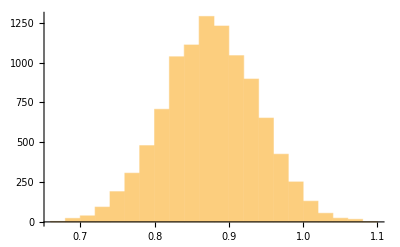

{0.750486,0.875755,0.0628223,-1.99401,9749}

```mathematica
nreps=10^4;
obs=gen[e]⟦pops,All,{1,2}⟧;
reps=Table[shuffle/@obs,{nreps}];
vl=N[Variance[Total/@Map[Total,#,{2}]]]&/@obs;
vlS=Table[N[Variance[Total/@Map[Total,#,{2}]]]&/@reps⟦j⟧,{j,nreps}];
vd=Sort[Mean/@vlS];
Histogram[vd]
mn=Mean[Mean/@vlS];mnObs=Mean[vl];sd=StandardDeviation[Mean/@vlS];{mnObs,mn,sd,(mnObs-mn)/sd,Length[Select[vd,#>Mean[vl]&]]}
```

This does the same for all 3 loci: again, the variance is lower (almost significantly)

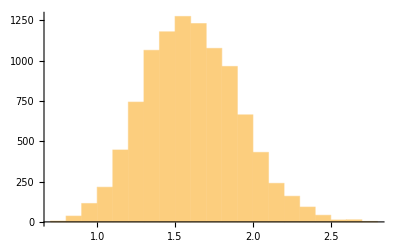

{1.04166,1.60706,0.301716,-1.87393,9775}

```mathematica
nreps=10^4;
pops=Union@@(pickPol[e,0.1,#]&/@{{1,2,3}});
obs=gen[e]⟦pops,All,{1,2,3}⟧;
reps=Table[shuffle/@obs,{nreps}];
vl=N[Variance[Total/@Map[Total,#,{2}]]]&/@obs;
vlS=Table[N[Variance[Total/@Map[Total,#,{2}]]]&/@reps⟦j⟧,{j,nreps}];
vd=Sort[Mean/@vlS];
Histogram[vd]
mn=Mean[Mean/@vlS];mnObs=Mean[vl];sd=StandardDeviation[Mean/@vlS];{mnObs,mn,sd,(mnObs-mn)/sd,Length[Select[vd,#>Mean[vl]&]]}
```

## Simulating clines

In principle, we need to follow haplotype frequencies at up to 4 loci.  This should be feasible using the machinery in “Simulations 2019”, but requires deciding on many parameters. Following the MS, I focus on WntA and optix. These control the shape of the forewing band, and the size of the red patch & rays, respectively.  Since LD is weak, it should be reasonable to focus on just these two loci.  Moreover, for both, to a first approximation, the lowland allele is dominant, so we may be able to deal with approximately four phenotypes.

Clines can be shifted for many reasons. LD tends to pull them together, but almost all deviations from symmetry will push them apart.
	- independent tension zones (eg +fds or under-dominance acting independently) will drift randomly and in general will be shifted - unless pulled together by LD or by a shared heterogeneous population structure. 
	- Synergistic costs (eg double heterozygotes being much less fit than expected) can force clines apart - examples from chromosome rearrangements (whwere acrocentrics may also arise)	
	- Asymmetric selection against recombinants (as in DMI models) cause clines to stagger.
	- + ve FDS can lead to establishment of arbitrary hybrid morphs.

We can distinguish neutral vs systematic shifting vs shifts that may occur in any direction.

Qualitatively, shifts tend to increase mean fitness - but there is no exact maximisation principle, even without FDS.

Note that because LD is weak, we can use just the marginal fitnesses of alleles at each locus. However, that will not correctly adress the dynamics, even if it is correct at equilibrium.

Reasonable models could be:
	1) Independent FDS on single genes, either additive, or by morph
	2) Two-locus models with fixed fitnesses - interaction between heterozygotes, and asymmetric selection against heterozygotes
	3) +ve FDS on four morphs, assuming that selection strongly favours the commonest morph, with a power law parameter that favours frequency in  synergistic way.  
	4) Modify this to distinguish heterozygotes etc
One should start both from coincidence and from a staggered initial point (staggering in both directions)

These are all toy models, which should be just illustrative.  Next, one needs to fit models more seriously:
- locus by locus looking at evidence of dominance
- two loci, checking how much LD is produced, and whether clines shift as observed

#### Simple two locus example.10

Two loci, multiplicative selection s=0.1, changing sign at x=0; 20+1+20 demes:

```mathematica
nd=20;s=0.1;pop0=stepCline[nd,{-5,5}];M=makeMendel[{1/2},{2,2}];
mig=makeM[0.5,41];
mw=multW[{{0,s},{0,s}}];
wl=Join[ConstantArray[1/mw,nd],{ConstantArray[1,{4,4}]},ConstantArray[mw,nd]];
```

40 generations:

```mathematica
pl=NestList[iterateCline[#,wl,M,mig]&,pop0,40];
```

Allele frequencies are the same at each locus.  This shows t=4, 40 (blue,black)

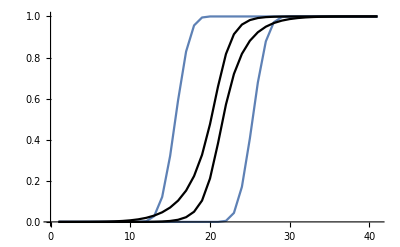

```mathematica
pp=Map[alleleFreqs[#,{2,2}]⟦All,2⟧&,pl,{2}];
Show[ListLinePlot/@Transpose[pp⟦5⟧],ListLinePlot[#,PlotStyle->Black]&/@Transpose[Last[pp]]]
```

#### Simple two locus example.10with FDS

```mathematica
nd=20;M=makeMendel[{1/2},{2,2}];mig=makeM[0.5,2nd+1];
```

Two loci, +ve selection m=1/2, s=0.2,  20+1+20 demes, starting shifted apart by ±2.5.  The clines pull together as a result of LD (blue→red at t=400):

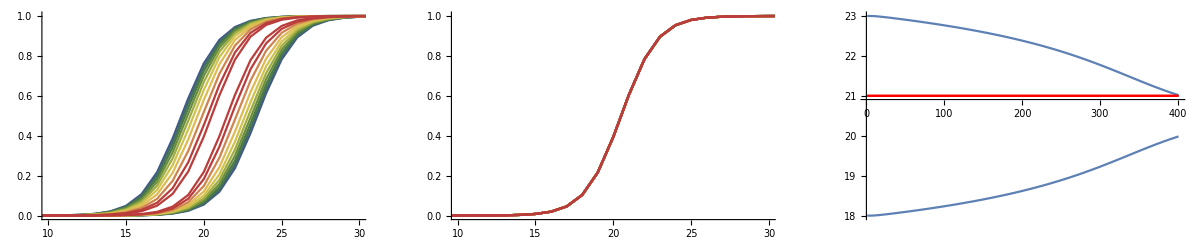

```mathematica
popA=stepCline[nd,{-2.5,2.5}];popB=stepCline[nd,{0,0}];s=0.2;tm=400;dt=40;
plA=NestList[(pp=alleleFreqs[#,{2,2}]⟦All,2⟧&/@#;uu=Map[{(1-#)^2,2#(1-#),#^2}&,pp,{2}];
wl=fdsW[{{s,0,0},{s,0,0}},#]&/@uu;
iterateCline[#,wl,M,mig])&,popA,tm];plB=NestList[(pp=alleleFreqs[#,{2,2}]⟦All,2⟧&/@#;uu=Map[{(1-#)^2,2#(1-#),#^2}&,pp,{2}];
wl=fdsW[{{s,0,0},{s,0,0}},#]&/@uu;
iterateCline[#,wl,M,mig])&,popB,tm];
ppA=Map[alleleFreqs[#,{2,2}]⟦All,2⟧&,plA,{2}];ppB=Map[alleleFreqs[#,{2,2}]⟦All,2⟧&,plB,{2}];
cf=ColorData["DarkRainbow"];
GraphicsRow[Append[Show[Table[ListLinePlot[#,PlotStyle->cf[t/tm]]&/@Transpose[#⟦t+1⟧],{t,dt,tm,dt}],PlotRange->{{10,30},{0,1}}]&/@{ppA,ppB},Show[ListLinePlot/@Transpose[Total/@ppA],ListLinePlot[#,PlotStyle->Red]&/@Transpose[Total/@ppB],PlotRange->All]]]
```

This is with dominance (for both fitness and FDS), s=0.1.  The clines move to the left at the same speed, and start too far apart to pull together:

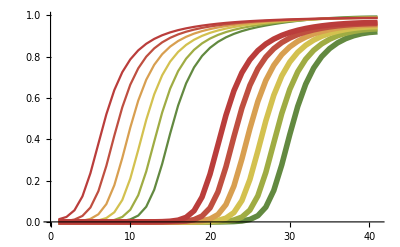

```mathematica
pop0=stepCline[nd,{0,15}];pl2=NestList[(pp=alleleFreqs[#,{2,2}]⟦All,2⟧&/@#;uu=Map[{(1-#)^2,2#(1-#),#^2}&,pp,{2}];
wl=fdsW[{{s,1,1},{s,1,1}},#]&/@uu;
iterateCline[#,wl,M,mig])&,pop0,400];
pop0=stepCline[nd,{-5,5}];
pp2=Map[alleleFreqs[#,{2,2}]⟦All,2⟧&,pl2,{2}];
Show[Table[{ListLinePlot[pp2⟦t+1,All,1⟧,PlotStyle->cf[t/400]],ListLinePlot[pp2⟦t+1,All,2⟧,PlotStyle->{Thickness[0.01],cf[t/400]}]},{t,150,400,50}]]
```

This shows similar simulations, but with the clines coinciding. Selection against the recessive allele is ineffective, so there is an asymmetric tail on the right. This takes time to develop.

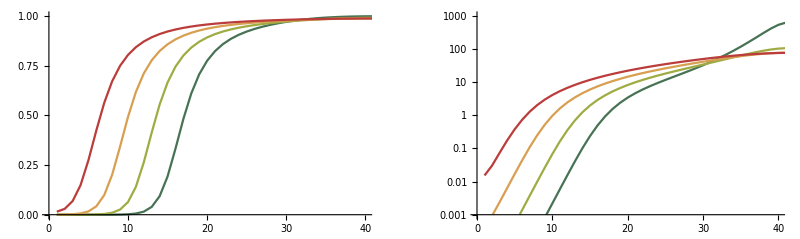

```mathematica
pop0=stepCline[nd,{0,0}];s=0.1;pl2=NestList[(pp=alleleFreqs[#,{2,2}]⟦All,2⟧&/@#;uu=Map[{(1-#)^2,2#(1-#),#^2}&,pp,{2}];
wl=fdsW[{{s,1,1},{s,1,1}},#]&/@uu;
iterateCline[#,wl,M,mig])&,pop0,400];
pp2=Map[alleleFreqs[#,{2,2}]⟦All,2⟧&,pl2,{2}];
GraphicsRow[{Show[Table[ListPlot[pp2⟦t+1,All,1⟧,Joined->True,PlotStyle->cf[t/400],PlotRange->{{0,40},{0,1}}],{t,100,400,100}]],Show[Table[ListLogPlot[pp2⟦t+1,All,1⟧/(1-pp2⟦t+1,All,1⟧),Joined->True,PlotStyle->cf[t/400],PlotRange->{{0,40},{0.001,1000}}],{t,100,400,100}]]}]
```

We would like to find a stable solution. One way to do this is to add a weak selection gradient, so that equilibrium is reached. One would have a selection that increases in strength linearly with position.  That is, employ multiplicative fitness against the dominant allele, with linear change in strength.  Here, with β=0.001, the clines settle at ~ -11, or counter selection -0.011. This is small relative to the selection 0.1 in the tails - though it will dominate over selection against recessives to the right,

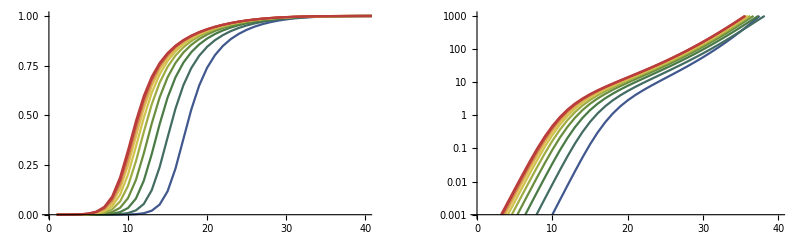

```mathematica
pop0=stepCline[nd,{0,0}];s=0.1;β=0.001;tm=1000;dt=100;
mwx[s_]:=multW[{{-s,s},{-s,s}}];
pl2=NestList[(pp=alleleFreqs[#,{2,2}]⟦All,2⟧&/@#;uu=Map[{(1-#)^2,2#(1-#),#^2}&,pp,{2}];
wl=MapThread[mwx[β #1]fdsW[{{s,1,1},{s,1,1}},#2]&,{Range[-nd,nd],uu}];
iterateCline[#,wl,M,mig])&,pop0,tm];
pp2=Map[alleleFreqs[#,{2,2}]⟦All,2⟧&,pl2,{2}];
GraphicsRow[{Show[Table[ListPlot[pp2⟦t+1,All,1⟧,Joined->True,PlotStyle->cf[t/tm],PlotRange->{{0,40},{0,1}}],{t,dt,tm,dt}]],Show[Table[ListLogPlot[pp2⟦t+1,All,1⟧/(1-pp2⟦t+1,All,1⟧),Joined->True,PlotStyle->cf[t/tm],PlotRange->{{0,40},{0.001,1000}}],{t,dt,tm,dt}]]}]
```

Now, try FDS for the four morphs that are expressed with complete dominance.  Here, if the clines start far apart (±15, left) they move in parallel and stay shifted.  However, if they start closer (<10 apart), they pull together, presumably through a combination of LD and swamping of the hybrid morph.  Even when they start apart, they will eventually pull together, but this takes a very long time.

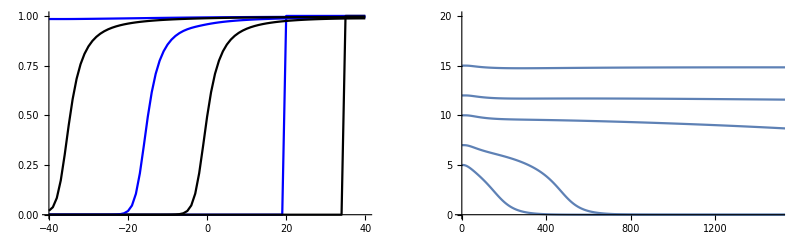

```mathematica
GraphicsRow[{makeClineGraph[makePdom[0.1,0,40,2000,{20,35}],1000,{Blue,Black}],Show[makePosGraph[makePdom[0.1,0,40,2000,{#,35}],PlotRange->{{0,1500},{0,20}}]&/@{20,22.5,25,27.5,30}]}]
```

If we impose a weak selection gradient to pin the clines (balancing extrinsic selection against dominance), then the clines are pushed together.  After 2000 generations, the cline position has not quite equilibrated, but is consistent with the counter selection βx=0.011 identified above

```mathematica
GraphicsRow[{makeClineGraph[makePdom[0.1,0.00025,40,2000,{20,35}],200,{Blue,Black}],Show[makePosGraph[makePdom[0.1,0.00025,40,2000,{#,35}],PlotRange->{{0,1500},{0,20}}]&/@{20,22.5,25,27.5,30}]}]
```

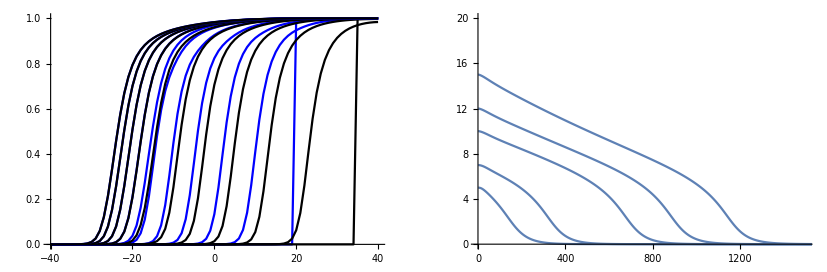

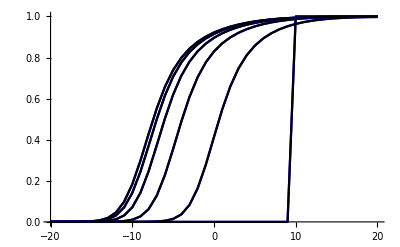

```mathematica
makeClineGraph[makePdom[0.1,0.001,20,1000,{10,10}],200,{Blue,Black}]
```

#### Relation between R_max and s for two-locus models with dominance: R~0.73s

```mathematica
nd=40;
tt=Table[(gg=makeClineDom[s,0.001,nd,1000,{nd-10,nd-10}];
pp=makePdom[s,0.001,nd,1000,{nd-10,nd-10}];
ww=1/Max[Drop[pp⟦-1,All,1⟧,1]-Drop[pp⟦-1,All,1⟧,-1]];
dl=MapThread[(#2⟦4⟧-(#1⟦1⟧)^2)/(#1⟦1⟧(1-#1⟦1⟧))&,Last/@{pp,gg}];intD=Interpolation[dl];{s,FindMaximum[intD[x],{x,nd/2,1,nd}]⟦1⟧,ww}),{s,0.05,0.3,0.05}];
TableForm[Prepend[tt,{"s","R_max","w"}]]
```

s | R_max | w
0.05 | 0.0438807 | 9.87229
0.1 | 0.074475 | 7.69013
0.15 | 0.104376 | 6.47688
0.2 | 0.13307 | 5.76764
0.25 | 0.159331 | 5.34332
0.3 | 0.185075 | 4.84646

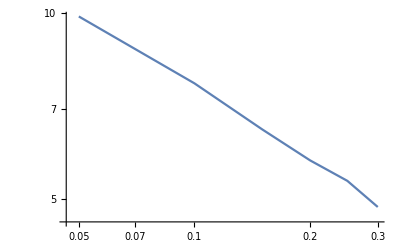

1.15178-0.381152 ls

```mathematica
ListLogLogPlot[tt⟦All,{1,3}⟧,Joined->True]
Fit[Log[tt⟦1;;-4,{1,3}⟧],{1,ls},ls]
```

We have that w ~ 2.5 √s~ 3.53σ √s or ~ √(12σ^2/s)

```mathematica
tt⟦All,3⟧√tt⟦All,1⟧
```

{2.20751,2.43183,2.50848,2.57937,2.67166,2.65451}

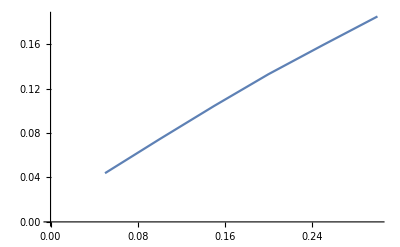

{0.647328 s,0.722797 s,-0.721261+0.807047 s}

```mathematica
ListLinePlot[tt]
{Fit[tt,{s},s],Fit[Drop[tt,-3],{s},s],Fit[tt//Log,{1,s},s]}
```

#### Summary so far

It seems that there are several forces acting on clines maintained by +ve FDS:
	- dominance causes a systematic movement
	- heterogeneous density or adaptation to different environments at these loci could  pin clines; the former is more likely
	- LD will pull overlapping clines together
	- A shift will be generated by selection 
	- FDS can maintain a hybrid morph, but if it is symmetric, there is no force maintaining

## Definitions

### Raw data

#### m,e

```mathematica
m::usage="m denotes melpomene; protected";
e::usage="e denotes erato; protected";
Protect[m,e];
```

#### erato

```mathematica
rawData[e]={{{Site1,CAM016702,0,0,1,1,1,1,0,0},
{Site1,CAM016703,0,0,1,1,1,1,0,0},
{Site1,CAM016704,0,0,1,1,1,1,0,0},
{Site1,CAM016705,0,0,1,1,1,0,0,0},
{Site1,CAM016706,0,0,1,1,1,1,0,0},
{Site1,CAM016707,0,0,1,1,1,1,0,0},
{Site1,CAM016708,0,0,1,1,1,1,0,0},
{Site1,CAM016709,0,0,1,1,1,1,0,0},
{Site1,CAM016710,0,0,1,1,1,1,0,0},
{Site1,CAM016711,0,0,1,1,1,1,0,0},
{Site1,CAM016712,0,0,1,1,1,1,0,0},
{Site1,CAM016713,0,0,1,1,1,1,0,0}},
{{Site2,CAM016045,0,0,1,1,1,1,0,0},
{Site2,CAM016046,0,0,1,1,1,0,0,0},
{Site2,CAM016047,0,0,1,0,1,1,0,0},
{Site2,CAM016048,0,0,1,1,1,1,0,0},
{Site2,CAM016872,0,0,1,1,1,1,0,0},
{Site2,CAM016873,0,0,1,1,1,1,0,0},
{Site2,CAM016875,0,0,1,1,1,1,0,0},
{Site2,CAM016876,0,0,1,1,1,1,0,1},
{Site2,CAM016877,0,0,1,1,0,0,0,0},
{Site2,CAM016879,0,0,1,1,0,1,0,0},
{Site2,CAM016881,0,0,1,1,1,1,0,0},
{Site2,CAM016882,0,0,1,1,0,1,0,0},
{Site2,CAM016883,0,0,1,1,0,1,0,0},
{Site2,CAM016885,0,0,1,1,1,1,0,0},
{Site2,CAM016886,0,0,1,1,1,1,0,0},
{Site2,CAM016898,0,0,1,1,1,1,0,0},
{Site2,CAM016899,0,0,1,1,1,1,0,0},
{Site2,CAM016900,0,0,1,1,1,1,0,0},
{Site2,CAM016901,0,0,1,1,1,1,0,0},
{Site2,CAM017320,0,0,1,1,1,0,0,0},
{Site2,CAM016736,0,0,1,1,1,1,0,0}},
{{Site3,CAM016079,0,0,1,1,1,0,0,1},
{Site3,CAM016410,0,0,1,1,0,0,1,1},
{Site3,CAM016415,0,0,1,1,0,1,0,1},
{Site3,CAM017191,0,0,1,1,0,1,0,0},
{Site3,CAM017192,0,0,1,1,1,1,0,1},
{Site3,CAM017201,0,0,1,1,0,0,0,1},
{Site3,CAM017206,0,0,1,1,1,0,0,1}},
{{Site4,CAM016110,0,0,1,1,0,1,0,1},
{Site4,CAM016112,0,0,1,1,0,1,0,1},
{Site4,CAM016813,0,0,1,1,0,1,1,0},
{Site4,CAM016816,0,0,1,1,0,1,1,0},
{Site4,CAM016924,0,0,1,1,0,0,1,1},
{Site4,CAM016927,0,0,1,1,1,1,1,1}},
{{Site5,CAM016088,0,0,1,1,0,0,0,1},
{Site5,CAM016091,0,0,1,1,0,0,0,1},
{Site5,CAM016094,0,0,1,1,0,0,0,0},
{Site5,CAM016096,0,0,1,1,0,0,1,0},
{Site5,CAM016099,0,0,1,1,1,1,1,0},
{Site5,CAM016740,0,0,1,1,0,1,1,1},
{Site5,CAM016741,0,0,1,1,0,1,0,1},
{Site5,CAM016744,0,0,1,1,1,1,0,0},
{Site5,CAM016745,0,0,1,0,0,1,1,1},
{Site5,CAM016749,0,1,0,1,1,1,0,1}},
{{Site6,CAM016302,0,0,1,1,1,0,1,1},
{Site6,CAM016303,0,0,1,1,1,0,0,1},
{Site6,CAM016307,0,0,1,0,1,1,1,1},
{Site6,CAM016308,0,0,1,0,0,1,0,1},
{Site6,CAM016310,0,0,1,1,0,1,0,1},
{Site6,CAM016311,0,0,1,1,0,0,1,1},
{Site6,CAM016314,0,0,1,1,1,0,0,1},
{Site6,CAM016316,0,0,1,1,0,1,1,0},
{Site6,CAM016317,0,0,1,1,0,1,1,1},
{Site6,CAM017218,0,0,1,1,0,1,1,1},
{Site6,CAM017220,0,0,1,1,1,0,1,1},
{Site6,CAM017222,0,0,1,1,1,1,1,1},
{Site6,CAM017224,0,0,1,1,0,1,1,1},
{Site6,CAM017225,0,0,1,1,0,1,1,1},
{Site6,CAM017226,0,0,1,1,0,0,1,1},
{Site6,CAM017229,0,0,1,1,1,1,1,1},
{Site6,CAM017230,0,0,0,1,1,1,1,1},
{Site6,CAM017234,0,0,1,0,1,0,1,1},
{Site6,CAM017235,0,0,1,1,0,0,0,1}},
{{Site7,CAM016637,0,0,1,1,0,0,0,0},
{Site7,CAM017342,0,0,0,1,1,1,0,0},
{Site7,CAM016049,0,0,1,1,1,1,1,1},
{Site7,CAM016051,0,0,1,1,0,1,1,1},
{Site7,CAM016052,0,0,1,0,1,0,1,0},
{Site7,CAM016053,0,0,1,1,1,1,1,1},
{Site7,CAM016054,0,0,1,1,0,1,1,1},
{Site7,CAM016634,0,0,1,1,0,1,1,1},
{Site7,CAM016635,0,0,1,1,0,1,1,1},
{Site7,CAM016636,0,0,1,1,0,0,0,1},
{Site7,CAM016638,0,0,0,1,0,1,1,1},
{Site7,CAM016639,0,0,1,1,0,0,1,1},
{Site7,CAM016640,0,0,1,0,1,0,1,1},
{Site7,CAM016641,0,0,1,1,1,0,1,1},
{Site7,CAM016642,0,0,1,1,0,1,1,0},
{Site7,CAM016643,0,0,1,1,1,0,1,1},
{Site7,CAM016644,0,0,1,1,1,1,1,1},
{Site7,CAM016645,0,1,1,1,1,0,1,1},
{Site7,CAM016646,0,0,1,1,1,1,0,1},
{Site7,CAM016647,0,0,1,1,0,1,1,1},
{Site7,CAM016648,0,0,0,1,1,1,0,1},
{Site7,CAM016649,0,0,1,1,1,1,0,1},
{Site7,CAM016650,0,0,1,1,0,0,1,1},
{Site7,CAM016651,0,0,0,0,0,0,1,1},
{Site7,CAM016652,0,0,1,1,1,1,1,1},
{Site7,CAM016664,0,0,1,1,1,1,0,1},
{Site7,CAM016665,0,0,0,1,0,1,1,1},
{Site7,CAM016666,0,0,0,1,0,0,1,1},
{Site7,CAM016667,0,0,1,1,0,0,1,1},
{Site7,CAM016668,0,0,1,1,0,0,1,1},
{Site7,CAM016669,0,0,0,0,0,1,1,1},
{Site7,CAM016670,0,0,1,1,0,0,1,1},
{Site7,CAM016671,0,0,1,1,1,1,0,1},
{Site7,CAM016681,0,0,0,1,0,1,1,1},
{Site7,CAM017328,1,0,1,1,1,1,0,1},
{Site7,CAM017330,1,0,1,0,0,0,1,1},
{Site7,CAM017331,0,0,0,1,1,1,1,1},
{Site7,CAM017332,0,0,1,1,0,0,1,1},
{Site7,CAM017333,0,0,1,1,1,1,1,1},
{Site7,CAM017334,0,0,1,1,0,0,1,1},
{Site7,CAM017337,0,0,1,1,0,0,1,1},
{Site7,CAM017338,0,0,1,1,0,0,1,1},
{Site7,CAM017339,0,0,1,1,1,1,0,1},
{Site7,CAM017340,0,0,1,1,0,1,1,1},
{Site7,CAM017341,0,0,1,1,1,1,0,1},
{Site7,CAM017343,0,1,1,1,0,0,1,1},
{Site7,CAM017346,0,0,1,1,1,1,1,1},
{Site7,CAM017347,0,0,0,1,1,1,1,1},
{Site7,CAM017348,0,0,1,1,0,0,1,1},
{Site7,CAM017349,0,0,1,1,0,0,0,1},
{Site7,CAM017350,0,0,1,1,0,0,1,1},
{Site7,CAM017604,0,1,1,1,1,0,1,1},
{Site7,CAM017606,0,0,1,1,0,1,1,0},
{Site7,CAM017607,0,0,1,1,0,0,1,1},
{Site7,CAM017608,1,0,1,1,0,1,1,1},
{Site7,CAM017609,0,0,1,1,0,1,0,1},
{Site7,CAM017610,0,0,1,1,0,0,1,1},
{Site7,CAM016019,1,1,1,1,0,0,1,1},
{Site7,CAM016020,0,0,1,1,0,1,1,1},
{Site7,CAM016021,0,0,1,1,0,0,1,1},
{Site7,CAM016022,0,0,0,1,0,0,1,1},
{Site7,CAM016023,1,0,1,1,1,1,1,1},
{Site7,CAM016024,0,0,1,1,0,0,1,1},
{Site7,CAM016025,0,0,1,1,0,1,1,1},
{Site7,CAM016026,0,0,1,1,0,0,1,1},
{Site7,CAM016027,0,0,0,1,0,0,1,1},
{Site7,CAM016028,0,0,1,1,0,1,1,1},
{Site7,CAM016029,0,0,0,1,1,1,1,1},
{Site7,CAM016030,0,0,1,0,0,0,1,1},
{Site7,CAM016031,0,0,0,1,0,0,1,1},
{Site7,CAM016032,1,0,1,1,0,0,1,1},
{Site7,CAM016033,1,0,1,0,1,1,1,1},
{Site7,CAM016034,0,0,1,1,1,1,1,1},
{Site7,CAM016035,0,0,1,1,0,0,1,1},
{Site7,CAM016521,0,0,0,1,0,0,1,1},
{Site7,CAM016522,0,0,1,1,0,0,1,1},
{Site7,CAM016523,0,0,1,1,0,0,1,1},
{Site7,CAM016524,0,0,0,0,0,0,1,1},
{Site7,CAM016525,0,0,0,1,0,0,1,1},
{Site7,CAM016526,0,1,1,0,0,0,1,1},
{Site7,CAM016527,0,0,1,1,0,1,1,1},
{Site7,CAM017141,0,0,0,1,0,1,1,1},
{Site7,CAM017142,0,0,1,1,1,0,1,1},
{Site7,CAM017143,0,0,1,1,0,1,1,1},
{Site7,CAM017144,0,1,1,1,0,1,1,1},
{Site7,CAM017145,0,0,1,0,1,0,1,1},
{Site7,CAM017146,0,0,0,1,0,1,1,1},
{Site7,CAM017147,0,0,1,0,1,1,1,1},
{Site7,CAM017148,0,0,1,1,0,1,1,1},
{Site7,CAM017149,0,0,0,0,0,0,1,1},
{Site7,CAM017150,0,0,1,1,0,0,1,1},
{Site7,CAM017151,0,0,0,1,1,1,1,1},
{Site7,CAM017296,0,1,1,0,0,1,0,1},
{Site7,CAM017297,0,0,1,1,0,0,1,1},
{Site7,CAM017298,0,0,0,1,1,0,1,1},
{Site7,CAM017300,0,0,0,0,0,1,1,0},
{Site7,CAM017301,1,1,1,1,0,0,1,1},
{Site7,CAM017302,0,0,1,1,0,0,1,1},
{Site7,CAM017303,0,1,1,1,0,1,1,1},
{Site7,CAM017306,0,0,0,1,0,0,1,1},
{Site7,CAM017307,0,0,1,1,1,0,1,1},
{Site7,CAM017308,0,0,1,1,1,1,1,1},
{Site7,CAM017309,1,0,1,1,0,1,1,1},
{Site7,CAM017310,0,0,0,0,0,1,1,1},
{Site7,CAM017311,0,0,1,1,0,1,1,1},
{Site7,CAM017312,0,1,1,0,0,1,1,1},
{Site7,CAM017314,0,1,1,1,0,0,0,0},
{Site7,CAM017315,0,0,1,1,0,0,1,1},
{Site7,CAM017316,0,0,0,1,0,0,1,1},
{Site7,CAM017317,0,0,1,1,0,1,1,1},
{Site7,CAM017318,0,1,1,1,0,0,1,1},
{Site7,CAM017319,0,0,1,1,0,0,1,1},
{Site7,CAM017601,0,1,1,0,0,0,1,1},
{Site7,CAM017602,1,0,1,0,0,0,0,1},
{Site7,CAM017603,0,0,1,1,0,0,0,1}},
{{Site8,CAM017428,1,1,0,0,0,0,1,1},
{Site8,CAM016039,0,0,0,1,0,1,1,1},
{Site8,CAM016507,0,0,1,0,0,0,1,1},
{Site8,CAM016512,0,0,1,1,0,1,1,1},
{Site8,CAM016513,0,0,1,1,0,0,1,1},
{Site8,CAM016514,0,1,1,1,0,0,1,1},
{Site8,CAM016515,0,0,1,1,0,0,1,1},
{Site8,CAM016517,0,1,1,0,0,0,0,1},
{Site8,CAM016518,1,1,1,1,0,1,1,1},
{Site8,CAM016520,1,0,1,1,0,1,1,1},
{Site8,CAM017157,0,0,1,1,0,0,1,1},
{Site8,CAM017158,0,0,0,1,0,0,1,1},
{Site8,CAM017159,0,1,1,1,0,0,1,1},
{Site8,CAM017160,0,0,1,1,0,0,1,1},
{Site8,CAM017424,0,0,1,1,0,0,1,1},
{Site8,CAM017425,0,0,0,1,0,1,1,1},
{Site8,CAM017426,0,0,0,1,0,0,1,1},
{Site8,CAM017427,0,1,0,0,0,1,1,1},
{Site8,CAM017429,0,0,0,0,1,0,1,1},
{Site8,CAM017432,0,0,1,1,0,0,1,1},
{Site8,CAM017433,1,0,1,0,0,0,1,1},
{Site8,CAM017435,0,0,0,1,1,0,1,1},
{Site8,CAM017436,0,0,0,1,0,0,1,1},
{Site8,CAM017438,0,0,0,0,0,0,1,1},
{Site8,CAM017439,0,0,0,1,0,0,1,1},
{Site8,CAM017441,0,0,1,1,0,0,1,1},
{Site8,CAM017443,0,0,1,1,0,1,1,1},
{Site8,CAM017444,0,0,1,1,1,0,1,1},
{Site8,CAM017445,0,0,1,1,0,0,1,1},
{Site8,CAM017446,0,0,0,1,0,0,1,1},
{Site8,CAM017447,1,1,1,1,1,1,1,1}},
{{Site9,CAM016777,0,1,1,1,0,0,0,1},
{Site9,CAM016780,0,1,1,1,1,0,1,1},
{Site9,CAM016783,0,0,1,1,0,0,1,1},
{Site9,CAM016784,0,1,0,0,0,1,1,1},
{Site9,CAM016786,1,0,0,1,1,0,1,1},
{Site9,CAM016787,0,1,1,1,0,1,1,1},
{Site9,CAM016788,0,1,1,0,1,0,1,1},
{Site9,CAM016789,0,1,1,1,0,0,1,1},
{Site9,CAM016790,0,0,0,1,0,1,1,1},
{Site9,CAM016791,0,0,1,0,1,1,1,1},
{Site9,CAM016793,0,0,1,1,0,0,1,1},
{Site9,CAM016794,0,1,1,1,0,0,1,1},
{Site9,CAM016795,0,0,1,1,0,1,1,1},
{Site9,CAM016796,0,0,0,0,0,1,1,1}},
{{Site10,CAM016176,0,1,1,0,1,1,1,1},
{Site10,CAM016177,0,0,1,1,0,0,1,1},
{Site10,CAM016178,1,1,1,1,0,1,1,1},
{Site10,CAM016179,0,0,1,1,0,0,1,1},
{Site10,CAM016180,0,1,1,1,0,1,1,1},
{Site10,CAM016181,1,0,0,0,0,0,1,1},
{Site10,CAM016182,1,1,1,0,0,0,1,1},
{Site10,CAM016184,0,0,0,1,0,0,1,1},
{Site10,CAM016185,1,0,1,1,0,0,1,1},
{Site10,CAM016186,0,1,1,0,0,0,1,1},
{Site10,CAM016187,0,1,1,0,1,0,1,1},
{Site10,CAM016188,0,1,0,1,0,0,1,1},
{Site10,CAM016192,1,0,0,0,0,1,1,1},
{Site10,CAM016193,0,0,1,1,1,1,1,1},
{Site10,CAM016194,0,0,1,1,0,1,1,1},
{Site10,CAM017031,0,1,1,1,0,0,1,1},
{Site10,CAM017032,1,1,1,1,1,0,1,1},
{Site10,CAM017033,1,0,1,1,0,1,1,1},
{Site10,CAM017034,0,0,0,0,0,0,1,1},
{Site10,CAM017036,1,0,1,1,0,1,1,1},
{Site10,CAM017037,0,1,1,1,1,0,1,1},
{Site10,CAM017038,0,0,1,1,0,0,1,1},
{Site10,CAM017039,0,1,1,1,0,0,1,1},
{Site10,CAM017042,0,0,1,0,1,1,1,1},
{Site10,CAM017044,0,0,1,1,1,1,1,1},
{Site10,CAM017045,0,0,0,1,0,0,1,1},
{Site10,CAM017046,0,1,1,1,1,0,1,1},
{Site10,CAM017274,1,1,0,1,0,0,1,1},
{Site10,CAM017275,0,0,1,1,0,0,1,1},
{Site10,CAM017276,0,0,0,0,0,0,1,1},
{Site10,CAM017277,0,0,1,1,0,0,1,1}},
{{Site11,CAM016750,0,0,0,0,0,1,1,1},
{Site11,CAM016752,0,1,0,0,1,0,1,1},
{Site11,CAM016755,0,0,0,0,0,1,1,1},
{Site11,CAM016756,0,1,1,1,0,0,1,1},
{Site11,CAM016757,1,1,1,1,0,0,1,1},
{Site11,CAM016758,0,1,1,1,0,0,1,1},
{Site11,CAM016759,0,0,1,1,0,0,1,1},
{Site11,CAM016760,1,1,1,1,0,0,1,1},
{Site11,CAM016761,0,1,0,1,0,1,1,1},
{Site11,CAM016762,0,1,0,1,0,1,1,1},
{Site11,CAM016763,0,0,0,0,0,1,1,1},
{Site11,CAM016764,1,0,0,0,0,0,1,1},
{Site11,CAM016767,1,1,0,1,1,1,1,1},
{Site11,CAM016768,0,0,1,1,0,0,1,1},
{Site11,CAM016771,1,1,0,1,0,1,1,1}},
{{Site12,CAM016423,0,1,0,1,0,0,1,1},
{Site12,CAM016447,1,1,1,1,0,0,1,1},
{Site12,CAM016448,1,0,1,1,0,0,1,1},
{Site12,CAM016451,1,1,1,1,1,1,1,1},
{Site12,CAM016452,1,1,0,1,0,0,1,1},
{Site12,CAM016453,0,1,0,0,0,1,1,1},
{Site12,CAM016455,0,0,1,1,0,0,1,1},
{Site12,CAM016456,0,0,1,1,1,0,1,1},
{Site12,CAM016457,0,1,0,0,0,1,1,1},
{Site12,CAM016458,1,0,0,1,0,0,1,1},
{Site12,CAM016459,0,0,1,1,1,0,1,1},
{Site12,CAM016460,1,1,0,1,1,0,1,1},
{Site12,CAM016461,0,1,1,1,0,0,1,1},
{Site12,CAM016462,1,0,0,1,0,0,1,1},
{Site12,CAM016463,0,0,1,1,1,0,1,1},
{Site12,CAM016464,1,1,1,1,0,1,1,1},
{Site12,CAM016466,0,1,0,1,0,1,1,1},
{Site12,CAM016976,1,1,1,1,0,1,1,1},
{Site12,CAM016978,0,1,0,1,0,0,1,1},
{Site12,CAM016979,1,1,0,1,0,0,1,1},
{Site12,CAM016980,1,1,0,1,0,0,1,0},
{Site12,CAM016981,1,0,1,0,0,1,1,1},
{Site12,CAM016985,0,1,0,0,1,0,1,1},
{Site12,CAM016986,0,0,0,1,0,1,1,1},
{Site12,CAM016987,0,0,0,1,0,0,1,1},
{Site12,CAM016995,1,0,0,0,0,0,1,1},
{Site12,CAM016996,1,1,0,1,0,0,1,1},
{Site12,CAM016997,1,1,0,1,0,0,1,1},
{Site12,CAM017000,0,1,0,1,0,0,1,1},
{Site12,CAM017001,0,1,0,1,0,1,1,1},
{Site12,CAM017002,0,1,0,0,0,0,1,1},
{Site12,CAM017003,0,1,1,0,0,0,1,1},
{Site12,CAM017004,0,1,0,1,0,0,1,1},
{Site12,CAM017418,0,0,0,1,0,0,1,1},
{Site12,CAM017419,0,0,0,1,1,1,1,1},
{Site12,CAM017420,0,0,0,0,0,0,1,1},
{Site12,CAM017421,0,0,0,0,0,0,1,1},
{Site12,CAM017422,1,0,0,0,1,0,1,1}},
{{Site13,CAM017050,0,1,0,0,0,1,1,1},
{Site13,CAM017051,0,1,0,1,0,1,1,1},
{Site13,CAM017052,1,0,0,0,0,1,1,1},
{Site13,CAM017054,1,1,0,1,0,0,1,1},
{Site13,CAM017055,1,1,0,0,0,0,1,1},
{Site13,CAM017056,1,1,1,1,0,1,1,1},
{Site13,CAM017057,1,1,0,1,0,1,1,1},
{Site13,CAM017058,1,1,1,1,0,0,1,1},
{Site13,CAM017059,0,1,0,0,0,0,1,1},
{Site13,CAM017062,0,1,1,0,1,0,1,1},
{Site13,CAM017063,0,1,0,1,0,0,1,1},
{Site13,CAM017065,1,1,1,0,0,0,1,1},
{Site13,CAM017074,0,1,1,1,0,1,1,1},
{Site13,CAM017127,0,1,1,0,0,0,1,1},
{Site13,CAM017129,0,1,0,1,0,0,1,1},
{Site13,CAM017130,0,1,0,1,0,1,1,1},
{Site13,CAM017132,0,1,1,0,0,1,1,1},
{Site13,CAM017133,1,1,0,1,0,0,1,1},
{Site13,CAM017265,1,0,0,1,0,1,1,1},
{Site13,CAM017266,1,1,1,0,0,0,1,1},
{Site13,CAM017270,0,0,0,0,0,0,1,1},
{Site13,CAM017280,1,1,1,0,0,1,1,1},
{Site13,CAM017281,0,1,0,1,1,0,1,1},
{Site13,CAM016256,1,0,0,1,0,0,1,1},
{Site13,CAM016258,0,1,1,1,0,0,1,1},
{Site13,CAM016261,0,1,1,1,1,0,1,1},
{Site13,CAM016262,1,1,0,1,0,0,1,1},
{Site13,CAM016265,1,1,1,0,0,0,1,1},
{Site13,CAM016271,1,1,1,0,0,0,1,1}},
{{Site14,CAM016208,0,0,0,0,0,1,1,1},
{Site14,CAM016212,0,0,0,0,1,1,1,1},
{Site14,CAM016213,0,1,1,1,0,0,1,1},
{Site14,CAM016215,0,1,1,0,0,0,1,1},
{Site14,CAM016221,1,1,0,1,0,0,1,1},
{Site14,CAM016577,1,1,0,1,0,0,1,1},
{Site14,CAM016578,1,0,0,1,0,0,1,1},
{Site14,CAM016580,1,1,1,0,1,0,1,1},
{Site14,CAM016582,1,1,0,1,0,0,1,1},
{Site14,CAM016584,1,0,1,1,0,1,1,1},
{Site14,CAM016585,1,1,1,0,0,0,1,1},
{Site14,CAM016588,0,1,0,0,0,0,1,1},
{Site14,CAM016590,0,1,0,0,0,0,1,1},
{Site14,CAM016930,0,0,1,0,0,0,1,1},
{Site14,CAM016947,0,0,1,0,0,1,1,1},
{Site14,CAM016961,0,1,0,1,0,0,1,1},
{Site14,CAM016964,1,1,0,1,0,0,1,1},
{Site14,CAM016965,1,0,1,1,0,0,1,1},
{Site14,CAM016968,1,0,1,1,0,1,1,1},
{Site14,CAM016969,0,1,0,0,0,0,1,1},
{Site14,CAM016970,0,1,0,0,0,0,1,1}},
{{Site15,CAM017010,1,1,0,1,0,0,1,1},
{Site15,CAM017011,0,1,0,0,0,1,1,1},
{Site15,CAM017020,0,1,0,0,1,1,1,1},
{Site15,CAM017022,1,1,0,1,0,0,1,1},
{Site15,CAM017023,0,1,0,1,0,0,1,1},
{Site15,CAM017025,1,1,0,0,0,1,1,1},
{Site15,CAM017028,0,1,0,0,0,0,1,1},
{Site15,CAM017029,0,1,0,0,0,0,1,1},
{Site15,CAM017109,0,1,1,0,0,1,1,1},
{Site15,CAM017110,0,1,1,1,0,0,1,1},
{Site15,CAM017114,1,1,0,1,0,1,1,1},
{Site15,CAM017116,1,1,0,1,0,0,1,1},
{Site15,CAM017118,1,1,0,1,0,0,1,1},
{Site15,CAM017119,1,1,1,1,0,0,1,1},
{Site15,CAM017122,0,1,0,0,0,0,1,1}},
{{Site16,CAM016539,1,1,0,1,0,0,1,1},
{Site16,CAM016553,1,1,0,0,0,0,1,1},
{Site16,CAM016554,1,1,0,0,1,0,1,1},
{Site16,CAM016555,1,1,0,0,0,0,1,1},
{Site16,CAM016556,1,1,0,0,1,1,1,1},
{Site16,CAM016558,1,1,0,0,0,1,1,1},
{Site16,CAM016561,1,1,0,0,0,0,1,1},
{Site16,CAM016563,1,1,0,0,0,0,1,1},
{Site16,CAM016564,1,1,0,0,0,0,1,1},
{Site16,CAM016565,1,1,0,0,0,0,1,1},
{Site16,CAM017079,1,0,0,1,0,1,1,1},
{Site16,CAM017082,1,1,0,1,0,0,1,1},
{Site16,CAM017086,0,1,0,0,0,0,1,1},
{Site16,CAM017166,1,1,0,0,0,1,1,1},
{Site16,CAM017167,1,1,0,0,0,0,1,1},
{Site16,CAM017168,1,1,0,0,0,1,1,1},
{Site16,CAM017169,0,0,0,0,0,1,1,1},
{Site16,CAM017170,1,1,1,0,0,0,1,1},
{Site16,CAM017171,0,1,0,0,0,1,1,1},
{Site16,CAM017284,1,1,0,0,0,0,1,1},
{Site16,CAM017395,1,1,0,0,0,0,1,1},
{Site16,CAM017396,1,1,0,0,0,1,1,1},
{Site16,CAM017397,1,1,0,0,0,0,1,1},
{Site16,CAM017399,1,1,0,0,0,0,1,1},
{Site16,CAM016557,0,1,1,1,0,0,1,1},
{Site16,CAM016559,0,1,0,0,0,1,1,1},
{Site16,CAM016560,1,1,0,1,0,0,1,1},
{Site16,CAM016562,1,1,0,1,0,0,1,1},
{Site16,CAM016566,1,1,1,0,0,1,1,1},
{Site16,CAM017085,0,1,0,0,1,0,1,1},
{Site16,CAM017087,1,1,0,0,0,1,1,1},
{Site16,CAM017088,0,1,0,0,0,0,1,1},
{Site16,CAM017161,1,1,1,0,0,0,1,1},
{Site16,CAM017163,0,1,0,1,0,0,1,1},
{Site16,CAM017165,1,1,0,1,0,0,1,1},
{Site16,CAM017287,1,0,0,0,0,0,1,1},
{Site16,CAM017398,1,1,0,1,0,0,1,1}},
{{Site17,CAM017393,1,1,0,1,0,0,1,1},
{Site17,CAM017407,1,1,0,0,0,0,1,1},
{Site17,CAM017408,1,1,0,0,0,1,1,1},
{Site17,CAM017410,1,1,1,0,0,0,1,1},
{Site17,CAM017413,1,1,0,0,0,0,1,1},
{Site17,CAM017414,1,1,0,0,0,0,1,1},
{Site17,CAM017415,1,1,0,0,1,0,1,1},
{Site17,CAM017416,1,1,0,0,1,0,1,1}}};
```

```mathematica
rawLocs[e]={{1,6.020,1307.0},
{2,10.235,1233.0},
{3,29.250,995.0},
{4,29.410,988.0},
{5,32.000,955.0},
{6,32.480,953.0},
{7,37.700,914.0},
{8,43.590,947.0},
{9,42.915,931.0},
{10,44.890,845.0},
{11,48.070,931.0},
{12,51.020,824.0},
{13,58.020,635.5},
{14,60.380,579.0},
{15,67.240,459.0},
{16,73.850,440.0},
{17,81.225,377.0}};
```

Check that each cluster is from the same site:

```mathematica
Length/@Union/@rawData[e]⟦All,All,1⟧
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

#### melpomene

```mathematica
rawData[m]={{{Site_1,CAM016683,1,1,1,1,1,1,0,0},
{Site_1,CAM016684,1,1,1,1,1,1,0,0},
{Site_1,CAM016685,1,1,1,1,1,1,0,0},
{Site_1,CAM016686,1,1,1,1,1,0,0,0},
{Site_1,CAM016687,1,1,1,1,1,1,0,0},
{Site_1,CAM016690,1,1,1,1,1,1,0,0},
{Site_1,CAM016691,1,1,1,1,1,1,0,0},
{Site_1,CAM016692,1,1,1,1,1,1,0,0},
{Site_1,CAM016693,1,1,1,1,1,1,0,0},
{Site_1,CAM016694,1,1,1,1,1,1,0,0},
{Site_1,CAM016695,1,1,1,1,1,1,0,0},
{Site_1,CAM016696,1,1,1,1,1,1,0,0},
{Site_1,CAM016697,1,1,1,1,1,1,0,0},
{Site_1,CAM016698,1,1,1,1,1,1,0,0},
{Site_1,CAM016701,1,1,1,1,1,1,0,0}},
{{Site_2,CAM016287,1,1,1,1,1,1,0,0},
{Site_2,CAM016734,1,1,1,1,1,1,0,0},
{Site_2,CAM016737,1,1,1,1,1,1,0,0},
{Site_2,CAM016738,1,1,1,1,1,1,0,0},
{Site_2,CAM016739,1,1,0,0,1,1,0,0},
{Site_2,CAM017257,1,1,1,1,0,1,0,0},
{Site_2,CAM017352,1,1,0,1,1,1,0,0},
{Site_2,CAM017353,1,1,0,1,1,1,0,0},
{Site_2,CAM017356,1,1,1,1,0,1,0,0},
{Site_2,CAM017357,1,1,1,1,1,1,0,0},
{Site_2,CAM017363,1,1,1,1,1,1,0,0},
{Site_2,CAM017364,1,1,0,1,1,1,0,0},
{Site_2,CAM017371,1,1,1,1,1,1,0,0},
{Site_2,CAM017372,1,1,1,1,1,1,0,0},
{Site_2,CAM017373,1,1,1,1,1,1,0,0},
{Site_2,CAM017376,1,1,1,1,1,1,0,0}},
{{Site_3,CAM016323,1,1,1,1,0,1,0,0},
{Site_3,CAM016324,1,1,1,1,1,1,0,0},
{Site_3,CAM016338,0,1,1,1,1,1,0,0},
{Site_3,CAM016339,1,1,0,0,1,0,0,0},
{Site_3,CAM016340,1,1,1,1,0,1,0,0},
{Site_3,CAM016341,1,1,1,1,1,0,0,0},
{Site_3,CAM016347,1,1,0,1,1,1,0,0},
{Site_3,CAM016349,1,1,1,1,1,1,0,0},
{Site_3,CAM016350,1,1,1,1,0,0,0,0},
{Site_3,CAM016354,1,1,1,1,1,1,0,0},
{Site_3,CAM016355,1,1,0,1,1,1,0,0},
{Site_3,CAM016378,1,1,0,1,1,1,0,0}},
{{Site_4,CAM016066,1,1,0,1,0,0,0,0},
{Site_4,CAM016073,1,1,1,1,1,1,0,0},
{Site_4,CAM016393,1,1,1,1,1,1,1,0},
{Site_4,CAM016394,1,1,1,0,0,0,1,0},
{Site_4,CAM016422,1,1,1,1,0,1,1,1}},
{{Site_5,CAM016082,1,1,1,0,1,1,0,0},
{Site_5,CAM016404,1,1,1,1,1,1,0,0},
{Site_5,CAM016406,1,0,1,0,0,1,1,0},
{Site_5,CAM016407,1,1,0,0,0,0,1,0},
{Site_5,CAM016408,1,1,0,1,0,1,0,0},
{Site_5,CAM016409,1,1,1,0,0,1,0,1},
{Site_5,CAM017209,0,1,1,1,0,0,0,1}},
{{Site_6,CAM016111,1,1,1,1,0,0,1,0},
{Site_6,CAM016808,1,0,1,1,1,1,0,0},
{Site_6,CAM016809,1,1,1,1,1,1,1,0},
{Site_6,CAM016810,1,1,1,1,1,1,0,0},
{Site_6,CAM016819,1,1,1,1,1,0,1,0},
{Site_6,CAM016820,1,1,0,1,1,1,0,1},
{Site_6,CAM016923,1,1,0,1,0,0,1,1}},
{{Site_7,CAM016084,1,1,0,1,0,1,0,0},
{Site_7,CAM016087,0,1,0,0,1,1,1,0},
{Site_7,CAM016089,1,1,0,0,0,1,0,1},
{Site_7,CAM016092,1,1,1,0,0,0,0,0},
{Site_7,CAM016097,1,1,1,1,0,0,1,1},
{Site_7,CAM016098,1,1,0,0,0,1,0,1},
{Site_7,CAM016100,1,1,1,0,1,0,1,0}},
{{Site_8,CAM016012,1,1,1,1,1,0,0,0},
{Site_8,CAM016306,1,1,0,1,0,1,1,1},
{Site_8,CAM016309,1,1,1,0,1,1,0,0},
{Site_8,CAM016312,0,1,0,1,1,1,1,1},
{Site_8,CAM016313,1,1,0,1,0,0,1,0},
{Site_8,CAM017231,1,1,0,1,0,0,0,1},
{Site_8,CAM017232,1,1,0,1,1,1,1,1}},
{{Site_9,CAM016055,1,1,1,0,0,0,1,0},
{Site_9,CAM016654,1,1,1,0,0,0,0,1},
{Site_9,CAM016655,1,1,1,1,1,1,1,1},
{Site_9,CAM016656,0,1,1,1,1,1,1,1},
{Site_9,CAM016657,1,1,1,1,0,0,1,0},
{Site_9,CAM016658,1,1,1,0,1,1,0,0},
{Site_9,CAM016660,1,0,1,1,0,0,0,0},
{Site_9,CAM016661,1,0,0,1,0,0,1,1},
{Site_9,CAM016672,1,1,1,1,0,0,0,0},
{Site_9,CAM017329,1,1,0,1,0,0,1,1},
{Site_9,CAM017335,1,1,1,1,1,0,1,1},
{Site_9,CAM017345,1,1,1,1,1,0,1,1},
{Site_9,CAM017351,1,1,0,1,0,0,1,1},
{Site_9,CAM017605,1,1,0,0,1,0,0,1},
{Site_9,CAM017611,1,1,0,1,0,0,0,1}},
{{Site_10,CAM016861,1,1,1,0,0,0,0,1},
{Site_10,CAM016863,1,0,0,0,0,0,1,1},
{Site_10,CAM016865,1,0,0,0,0,1,1,1},
{Site_10,CAM016867,1,0,0,1,0,1,1,0},
{Site_10,CAM016869,1,1,1,0,1,0,0,0}},
{{Site_11,CAM016036,1,1,0,1,0,1,1,1},
{Site_11,CAM016500,1,0,0,1,0,0,1,1},
{Site_11,CAM016503,1,0,1,0,1,1,1,1},
{Site_11,CAM016505,1,0,0,0,0,0,1,1},
{Site_11,CAM016508,1,1,0,0,0,0,1,1},
{Site_11,CAM016509,1,1,0,0,0,0,1,1},
{Site_11,CAM016510,1,1,1,0,1,1,1,1},
{Site_11,CAM016511,1,1,0,0,0,0,0,1},
{Site_11,CAM017152,1,1,1,0,0,0,1,1},
{Site_11,CAM017153,1,1,1,0,0,0,0,1},
{Site_11,CAM017154,0,0,0,0,0,0,1,0},
{Site_11,CAM017155,1,1,1,1,0,0,1,1},
{Site_11,CAM017431,1,1,0,0,0,0,1,1},
{Site_11,CAM017437,0,1,0,0,0,0,1,1},
{Site_11,CAM017440,1,1,0,0,0,0,1,1}},
{{Site_12,CAM016189,0,1,1,0,1,0,1,1},
{Site_12,CAM016190,0,0,0,0,0,0,1,1},
{Site_12,CAM016191,1,1,0,0,0,0,1,1},
{Site_12,CAM016195,0,1,0,0,0,0,0,1},
{Site_12,CAM016196,1,0,0,0,0,0,1,1},
{Site_12,CAM017040,0,1,1,1,0,0,1,1},
{Site_12,CAM017041,1,0,0,0,0,0,1,1}},
{{Site_13,CAM016751,0,0,0,0,0,0,1,1},
{Site_13,CAM016753,0,0,0,0,0,0,0,1},
{Site_13,CAM016754,1,1,0,0,0,0,1,1},
{Site_13,CAM016765,1,1,0,0,0,0,1,1},
{Site_13,CAM016766,0,0,0,0,0,0,1,1},
{Site_13,CAM016769,1,1,0,0,0,0,1,1}},
{{Site_14,CAM016424,0,1,0,0,0,0,1,1},
{Site_14,CAM016426,0,0,0,0,0,0,1,0},
{Site_14,CAM016428,1,1,0,1,0,0,1,1},
{Site_14,CAM016465,0,0,0,0,0,0,0,1},
{Site_14,CAM016990,0,0,0,0,0,0,1,1}},
{{Site_15,CAM017053,0,0,0,1,0,0,1,1},
{Site_15,CAM017064,0,0,0,0,0,0,1,1},
{Site_15,CAM017067,1,0,0,0,0,0,1,1},
{Site_15,CAM017068,1,0,0,0,0,0,1,1},
{Site_15,CAM017069,0,0,0,1,0,0,1,1},
{Site_15,CAM017071,0,0,0,0,0,0,1,1},
{Site_15,CAM017128,0,1,0,0,0,0,1,1},
{Site_15,CAM017134,0,0,0,1,0,0,1,1},
{Site_15,CAM017136,0,0,0,0,0,0,1,1},
{Site_15,CAM017137,0,0,0,0,0,0,1,1},
{Site_15,CAM017264,0,1,1,1,0,0,1,1},
{Site_15,CAM017267,1,0,0,0,0,0,0,1},
{Site_15,CAM017268,0,0,0,0,0,0,1,1},
{Site_15,CAM017272,0,0,0,0,0,0,1,1},
{Site_15,CAM017282,0,1,0,0,0,0,1,1}},
{{Site_16,CAM016266,0,0,0,0,0,0,1,1},
{Site_16,CAM016267,0,0,0,0,0,0,1,1},
{Site_16,CAM016268,0,0,0,0,0,0,1,1},
{Site_16,CAM016270,1,0,0,0,0,0,1,1},
{Site_16,CAM016272,1,1,0,0,0,0,1,1}},
{{Site_17,CAM016197,0,0,1,0,0,0,0,1},
{Site_17,CAM016205,0,0,0,0,0,1,1,1},
{Site_17,CAM016595,0,1,0,0,0,0,1,1},
{Site_17,CAM016598,0,0,0,0,0,0,1,1},
{Site_17,CAM016599,0,0,0,0,0,0,1,1},
{Site_17,CAM016602,1,1,0,1,0,0,1,1},
{Site_17,CAM016606,0,0,0,0,0,0,1,1},
{Site_17,CAM016608,1,0,0,0,0,0,1,1},
{Site_17,CAM016609,0,0,0,0,0,0,1,1},
{Site_17,CAM016611,0,0,1,0,0,0,1,1},
{Site_17,CAM016954,0,0,0,0,0,0,1,1},
{Site_17,CAM016955,0,0,0,0,0,0,1,1},
{Site_17,CAM016956,0,0,0,0,0,0,1,1}},
{{Site_18,CAM017018,0,0,0,0,0,0,1,1},
{Site_18,CAM017019,0,0,0,0,0,0,1,1},
{Site_18,CAM017117,0,0,0,0,0,0,1,1},
{Site_18,CAM017121,0,0,0,0,0,0,1,1},
{Site_18,CAM017123,1,1,0,0,0,0,0,1},
{Site_18,CAM017125,1,0,0,0,1,1,1,1}},
{{Site_19,CAM016538,0,0,0,0,0,0,1,1},
{Site_19,CAM016540,0,0,0,0,0,0,1,1},
{Site_19,CAM016550,1,0,0,0,0,0,1,1},
{Site_19,CAM017080,0,1,0,0,0,0,1,1},
{Site_19,CAM017083,0,0,0,0,0,0,1,1},
{Site_19,CAM017084,1,0,0,0,0,0,1,1},
{Site_19,CAM017089,0,0,0,0,0,0,1,1},
{Site_19,CAM017090,1,0,0,0,0,0,1,1},
{Site_19,CAM017092,0,0,0,0,0,0,1,1},
{Site_19,CAM017093,0,0,0,0,0,0,1,1},
{Site_19,CAM017094,1,0,0,0,0,0,1,1},
{Site_19,CAM017095,0,0,0,0,0,0,1,1},
{Site_19,CAM017096,1,0,0,0,0,0,1,1},
{Site_19,CAM017099,0,0,0,0,0,0,1,1},
{Site_19,CAM017102,0,0,0,0,0,0,1,1},
{Site_19,CAM017103,0,0,0,0,0,0,1,1}}};
```

```mathematica
rawLocs[m]={{1,6.02,1307.0,15},
{2,11.82,1233.0,16},
{3,18.97,995.0,12},
{4,28.34,988.0,5},
{5,29.25,955.0,7},
{6,29.41,953.0,7},
{7,32.00,914.0,7},
{8,32.48,947.0,7},
{9,36.39,931.0,15},
{10,37.14,845.0,5},
{11,43.59,931.0,15},
{12,44.89,824.0,7},
{13,48.07,635.5,6},
{14,51.02,579.0,5},
{15,56.82,459.0,15},
{16,59.22,440.0,5},
{17,60.38,377.0,13},
{18,67.24,612.0,6},
{19,73.85,638.0,16}};
```

Check that each cluster is from the same site:

```mathematica
Length/@Union/@rawData[m]⟦All,All,1⟧
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

#### locusNames

```mathematica
locusNames[e]={"WntA","Ro","Cortex","Optix"};
locusNames[m]={"WntA","N","Cortex","Optix"};
```

### Setting up data: codes, nPops,gen, freqs, x, z

#### codes

```mathematica
codes::usage="codes[e] gives the individual codes for erato, clustered by site";
codes[s:(e|m)]:=codes[s]=rawData[s]⟦All,All,2⟧;
```

#### gen, freqs

```mathematica
swapAlleles::usage="swapAlleles[e][{{0,0},{0,1},{1,0},{1,1}}] swaps allele labels for loci 2, 3 (Ro, Cortex) in erato so that alleles are all aligned; in melpomene, labels 1,2,3 (WntA,Ro,Cortex) are swapped";
swapAlleles[e][{g1_,g2_,g3_,g4_}]:={g1,1-g2,1-g3,g4};swapAlleles[m][{g1_,g2_,g3_,g4_}]:={1-g1,1-g2,1-g3,g4};
```

```mathematica
gen::usage="gen[e] gives the diploid genotypes, {{0,1},…}, clustered by site. Loci are in order WntA, Ro, Cortex, Optix. Allele labels for Ro, Cortex are swapped so that frequencies increase with x.  ";
gen[s:(e|m)]:=gen[s]=Map[swapAlleles[s][Partition[#,2]]&,rawData[s]⟦All,All,3;;-1⟧,{2}];
```

```mathematica
freqs::usage="freqs[{{{0,1},…},…}] gives the allele frequencies at the 4 loci. freqs[e] gives the frequencies for all the erato samples";
freqs[pop:{{{0|1,0|1}..}...}]:=Mean/@Mean[pop];
freqs[s:(e|m)]:=freqs[s]=freqs/@gen[s];
```

#### x, z

```mathematica
x::usage="x[e] gives the position of the sites along the transect";
x[s:(e|m)]:=x[s]=rawLocs[s]⟦All,2⟧;
```

```mathematica
z::usage="z[e] gives the altitude of the sites";
z[s:(e|m)]:=z[s]=rawLocs[s]⟦All,3⟧;
```

#### nPops, nInds

```mathematica
nPops::usage="nPops[e] gives the number of sampled populations for erato";
nPops[s:(e|m)]:=nPops[s]=Length[gen[s]];
```

```mathematica
nInds::usage="nInds[e] gives the number of individuals in each sample for erato";
nInds[s:(e|m)]:=nInds[s]=Length/@gen[s];
```

#### types, typeArray, genFreqs

```mathematica
types::usage="types gives the three diploid genotypes {{0,0},{0,1},{1,1}} at a single locus";types={{0,0},{0,1},{1,1}};
```

```mathematica
typeArray::usage="typeArray[k] gives a k dimensional array of the possible diploid genotypes at k loci";
typeArray[k_Integer]:=typeArray[k]=Outer[List,Sequence@@ConstantArray[types,k],1];
```

```mathematica
genFreqs::usage="genFreqs[e,{2,3}] stores the genotype frequencies at loci {2,3}, in the form {{n_00,n_01,n_02},…}, for each sub-population. genFreqs[{{{0,0},{0,1},…},…},{2,3}] gives the genotype frequencies in pop at loci {2,3}";
genFreqs[pop_List,loci:{___Integer}]:=Module[{k=Length[loci]},
Map[Count[Map[Sort,pop⟦All,loci⟧,{2}],#]&,typeArray[k],{k}]];
genFreqs[s:(e|m),loci:{___Integer}]:=genFreqs[s,loci]=
(genFreqs[#,loci]&/@gen[s]);
```

### Deviations from HW: likHW, Fis

#### likHW, Fis

```mathematica
nLog[0|0.]:=0;
nLog[x_]:=x Log[x];
```

```mathematica
likHW[{0,0,_}][_]:=Indeterminate;
likHW[{_,0,0}][_]:=Indeterminate;
likHW[{n0_,n1_,n2_}][f_]:=Module[{n=n0+n1+n2,p,q},
p=(n2+n1/2)/n;q=1-p;
n Log[n]-nLog[n0]-nLog[n1]-nLog[n2]+n0 Log[q^2+pqf]+n1 Log[2pq(1-f)]+n2 Log[p^2+pqf]];
```

```mathematica
Fis[{0,0,_}]:=Indeterminate;
Fis[{_,0,0}]:=Indeterminate;
Fis[{n0_,n1_,n2_}]:=1-((n0+n1+n2)n1)/(2(n0+n1/2)(n2+n1/2));
```

#### pCline

```mathematica
pCline::usage="pCline[TraditionalForm`";
pCline[{p0_,p1_,w_,y_}][x_]:=Module[{},
p0+(p1-p0)/(1+Exp[-4(x-y)/w])];
```

#### seln

```mathematica
seln::usage="seln[p,h_1,h_2] gives the selection coefficient in a model of FDS with dominanxce";
seln[p_,h1_,h2_]:=((2p-1)+2p(1-p)h2)(1-h1(2p-1));
```

#### pClineDom

```mathematica
pClineDom::usage="pClineDom[TraditionalForm`";
pClineDom[{h1_,h2_,w_,y_},ϵ_][xx_]:=Module[{p,wy=widthCline[h1,h2,ϵ],xs,sol,xmin},
xs=(xx-y) wy⟦1⟧/w+wy⟦2⟧;
sol=solnCline[speed[h1,h2],h1,h2,ϵ];
xmin=x[ϵ]/.sol;
If[xs<xmin,0,If[xs>0,1,p/.FindRoot[xs==x[p]/.sol,{p,0.5,0,1-ϵ}]]]];
```

#### widthCline

```mathematica
widthCline::usage="widthCline[h_1,h_2,ϵ] stores the cline width and centre in scaled units";
```

```mathematica
widthCline[h1_,h2_,ϵ_]:=widthCline[h1,h2,ϵ]=Module[{fm,pm,ss=solnCline[speed[h1,h2],h1,h2,ϵ]},
fm=FindMaximum[y[p]/.ss,{p,0.5,0,1-ϵ}];
pm=p/.fm⟦2⟧;{1/fm⟦1⟧,x[pm]/.solnCline[speed[h1,h2],h1,h2,ϵ]}];
```

#### pr

```mathematica
pr::usage="pr[F,p,j,n] gives the probability of sampling j from n, with binomial sampling from an underlying Beta";
pr[f_,p_,j_Integer,n_Integer]:=Module[{α=1/f-1},Binomial[n,j] Beta[α p+j,α (1-p)+n-j]/Beta[α p,α (1-p)]];
pr[0|0.,p_,j_Integer,n_Integer]:=
Binomial[n,j] p^j(1-p)^(n-j);
```

#### likCline

```mathematica
likCline::usage="likCline[{{x_1,n_1,j_1},…},{p_0,p_1,w,y,F}] gives the log likelihood of a sigmoid cline";
likCline[{x_,n_Integer,j_Integer},{p0_,p1_,w_,y_,F_}]:=Module[{},
Log[pr[F,pCline[{p0,p1,w,y}][x],j,n]]];
likCline[xnj:{{_,_Integer,_Integer}...},{p0_,p1_,w_,y_,F_}]:=
Total[likCline[#,{p0,p1,w,y,F}]&/@xnj];
```

#### likClineDom

```mathematica
likClineDom::usage="likClineDom[{{x_1,n_1,j_1},…},{h_1,h_2,w,y,F}] gives the log likelihood of a cline maintained by +ve FDS, with dominance coefficients h_1,h_2";
likClineDom[{x_,n_Integer,j_Integer},{h1_,h2_,w_,y_,F_}]:=Module[{ϵ=10^-4},
Log[pr[F,pClineDom[{h1,h2,w,y},ϵ][x],j,n]]];
likClineDom[xnj:{{_,_Integer,_Integer}...},{h1_,h2_,w_,y_,F_}]:=
Total[likClineDom[#,{h1,h2,w,y,F}]&/@xnj];
```

```mathematica
locusNames[e]
```

{WntA,Ro,Cortex,Optix}

### LD: rangeD, rangeR, likD, likR, expG, mleD, likDTable

#### rangeD

```mathematica
rangeD::usage="rangeD[{p_1,p_2}] gives the allowed range of D";
rangeD[{p1_,p2_}]:={-Min[p1 p2,(1-p1)(1-p2)],Min[p1(1-p2),(1-p1)p2]};
```

#### likD

```mathematica
likD::usage="likD[{{g_00,…},…},{p_1,p_2,D}] gives the log likelihood, relative to a perfect fit.";
likD[g_List,ppd:{_,_,_}]:=Module[{ex=expG[ppd],fg=Flatten[g],n},
n=Total[fg];n Log[n]-Total[nLog/@fg]+fg.Log[Flatten[ex]]];
```

#### expG

```mathematica
expG::usage="expG[{p_1,p_2,D}] gives the expected genotype frequencies at two loci";
expG[{p1_,p2_,d_}]:=Module[{q1=1-p1,q2=1-p2,h00,h01,h10,h11},
h00=q1 q2+d;h01=q1 p2-d;h10=p1 q2-d;h11=p1 p2+d;
{{h00^2, 2h00 h01, h01^2}, {2h00 h10, 2(h00 h11+h01 h10), 2h01 h11}, {h10^2, 2h10 h11, h11^2}}];
```

#### mleD

```mathematica
mleD::usage="mleD[{{g_00,…},…}] gives {L_(D = 0),L̂,D̂}";
mleD[g_List]:=Module[{n=Total[Flatten[g]],pp,rd,ϵ=10^-4,fm},
pp={(Total/@g),Total[g]}.{0,1/2,1}/n;
If[0<pp⟦1⟧<1&&0<pp⟦2⟧<1,
rd=rangeD[pp];
fm=FindMaximum[likD[g,Append[pp,d]],{d,0,rd⟦1⟧+ϵ,rd⟦2⟧-ϵ}];{likD[g,Append[pp,0]]//N,fm⟦1⟧,d/.fm⟦2⟧},
{Indeterminate}]];
```

#### likDTable

```mathematica
likDTable::usage="likDTable[e,{1,2}] gives a table of {pop,N,L_(D = 0),max(L),D̂}, for polymprphic sites";
likDTable[s_,loci_]:=DeleteCases[MapThread[Join[{#1,#2},mleD[#3]]&,{Range[nPops[s]],nInds[s],genFreqs[s,loci]}],{_,_,Indeterminate}];
```

#### rangeR

```mathematica
rangeR::usage="rangeR[e,7,{1,3}] gives the allowed range of R for site 7, loci {1,3}. rangeR[e,{1,3}] gives the allowed range for all polymorphic sites";
rangeR[s_,j_,loci_]:=Module[{pp=freqs[s]⟦j,loci⟧},If[0<pp⟦1⟧<1&&0<pp⟦2⟧<1,rangeD[pp]/(√(Times@@(pp(1-pp))))//N,Indeterminate]];
rangeR[s_,loci_]:=Module[{rr},
rr=Transpose[DeleteCases[Table[rangeR[s,j,loci],{j,nPops[s]}],Indeterminate]];
{Max[rr⟦1⟧],Min[rr⟦2⟧]}];
```

#### likR

```mathematica
likR::usage="likR[e,7,{1,3}][R] gives the log likelihood of R for site 7, loci {1,3}. likR[e,{1,3}] gives log(L), summed all polymorphic sites";likR[s_,j_,loci_][r_]:=Module[{pp=freqs[s]⟦j,loci⟧},If[0<pp⟦1⟧<1&&0<pp⟦2⟧<1,likD[genFreqs[s,loci]⟦j⟧,Append[pp,r √(Times@@(pp(1-pp)))]]//N,Indeterminate]];
likR[s_,loci_][r_]:=Total[DeleteCases[Table[likR[s,j,loci][r],{j,nPops[s]}],Indeterminate]];
```

#### mleR

```mathematica
mleR::usage="mleR[e,{1,2}] gives {L_(R = 0),L̂,R̂}, using all poolymorphic sites";
mleR[s:(e|m),loci_List]:=Module[{rr=rangeR[s,loci],ϵ=10^-4,fm},
fm=FindMaximum[likR[s,loci][r],{r,0,rr⟦1⟧+ϵ,rr⟦2⟧-ϵ}];
{likR[s,loci][0],fm⟦1⟧,r/.fm⟦2⟧}];
```

#### likRTable

```mathematica
likRTable::usage="likDTable[e] gives a table of {loci,L_(D = 0),max(L),R̂}, for polymorphic sites";
likRTable[s:(e|m)]:=Module[{ss=Subsets[Range[4],{2}]},
Prepend[mleR[s,#],locusNames[s]⟦#⟧]&/@ss];
```

#### pickPol

```mathematica
pickPol::usage="pickPol[e,h,{1,2}] picks the set of populations with √(SubscriptBox[p, 1] SubscriptBox[q, 1] SubscriptBox[p, 2] SubscriptBox[q, 2])>h.  ";
pickPol[s:(e|m),h_,loci_List]:=Module[{pp=freqs[s]⟦All,loci⟧},
Pick[Range[nPops[s]],(√(Times@@(#(1.-#)))>h)&/@pp]];
```

### Phenotype data

#### Raw data: erato

```mathematica
rawDataP[e]={{CAM016019,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016020,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016021,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016022,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016023,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016024,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016025,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016026,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016027,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016028,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016029,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016030,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016031,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016032,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016033,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016034,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016035,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016039,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM016045,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016046,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016047,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016048,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016049,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016051,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016052,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016053,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016054,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016079,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.346666667,77.96011667,995},
{CAM016088,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016091,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016094,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016096,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016099,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016102,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.42925,77.98665,991},
{CAM016105,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.42925,77.98665,991},
{CAM016110,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.409933333,77.91535,988},
{CAM016112,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.409933333,77.91535,988},
{CAM016114,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.459233333,77.8867,994},
{CAM016115,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.459233333,77.8867,994},
{CAM016121,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.459233333,77.8867,994},
{CAM016124,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.459233333,77.8867,994},
{CAM016128,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.475316667,77.87033333,856},
{CAM016129,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.475316667,77.87033333,856},
{CAM016138,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.475316667,77.87033333,856},
{CAM016139,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.475316667,77.87033333,856},
{CAM016140,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.475316667,77.87033333,856},
{CAM016145,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.41605,77.72901667,857},
{CAM016150,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.2408,77.96093333,939},
{CAM016151,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.2408,77.96093333,939},
{CAM016162,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.2456,77.90856667,638},
{CAM016163,m,opt(H)opt(L),WntA(H)WntA(L),Ro(H)__,1.2456,77.90856667,638},
{CAM016164,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.2456,77.90856667,638},
{CAM016167,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.246316667,77.94273333,750},
{CAM016168,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.246316667,77.94273333,750},
{CAM016169,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.246316667,77.94273333,750},
{CAM016170,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.246316667,77.94273333,750},
{CAM016171,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.246316667,77.94273333,750},
{CAM016172,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.246316667,77.94273333,750},
{CAM016174,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.2408,77.96093333,939},
{CAM016176,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016177,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM016178,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016179,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM016180,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016181,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.243283333,77.86008333,845},
{CAM016182,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016184,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016185,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016186,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016187,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016188,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016192,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM016193,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM016194,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM016208,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016212,m,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.115566667,77.77833333,579},
{CAM016213,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016215,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016221,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016226,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.5818,77.82098333,638},
{CAM016229,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.5818,77.82098333,638},
{CAM016231,m,opt(H)opt(L),WntA(H)WntA(L),Ro(H)__,1.5818,77.82098333,638},
{CAM016232,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.5818,77.82098333,638},
{CAM016233,f,opt(H)opt(L),WntA(L)WntA(L),Ro(H)__,1.5818,77.82098333,638},
{CAM016236,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.5818,77.82098333,638},
{CAM016256,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.250966667,77.69885,606},
{CAM016258,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.250966667,77.69885,606},
{CAM016261,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.250966667,77.69885,606},
{CAM016262,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.250966667,77.69885,606},
{CAM016265,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.250966667,77.69885,606},
{CAM016271,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.250966667,77.69885,606},
{CAM016302,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016303,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016307,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016308,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016310,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016311,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016314,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016316,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016317,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM016410,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.346666667,77.96011667,995},
{CAM016415,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.346666667,77.96011667,995},
{CAM016423,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016447,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016448,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016451,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016452,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016453,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.187816667,77.83105,824},
{CAM016455,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.187816667,77.83105,824},
{CAM016456,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.187816667,77.83105,824},
{CAM016457,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.187816667,77.83105,824},
{CAM016458,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016459,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.187816667,77.83105,824},
{CAM016460,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016461,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016462,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016463,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.187816667,77.83105,824},
{CAM016464,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016466,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016507,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM016512,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM016513,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM016514,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM016515,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM016517,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM016518,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM016520,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM016521,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016522,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016523,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016524,m,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.291033333,77.87736667,1064},
{CAM016525,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016526,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016527,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM016539,f,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016553,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016554,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016555,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016556,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016557,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM016558,f,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016559,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016560,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM016561,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016562,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM016563,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016564,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016565,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM016566,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM016577,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016578,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016580,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016582,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016584,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016585,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016588,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.115566667,77.77833333,579},
{CAM016590,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.115566667,77.77833333,579},
{CAM016634,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016635,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016636,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016637,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016638,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016639,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016640,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016641,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016642,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016643,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016644,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016645,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.306233333,77.90983333,839},
{CAM016646,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016647,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016648,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016649,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016650,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016651,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016652,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016664,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016665,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016666,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016667,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016668,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016669,f,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.306233333,77.90983333,839},
{CAM016670,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016671,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016681,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM016702,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016703,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016704,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016705,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016706,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016707,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016708,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016709,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016710,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016711,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016712,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016713,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.398016667,78.17813333,1307},
{CAM016736,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.459966667,78.0728,1227},
{CAM016740,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016741,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016744,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016745,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016749,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.38945,77.90103333,955},
{CAM016750,m,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.25185,77.8196,931},
{CAM016752,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.25185,77.8196,931},
{CAM016755,m,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.25185,77.8196,931},
{CAM016756,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.25185,77.8196,931},
{CAM016757,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.25185,77.8196,931},
{CAM016758,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.25185,77.8196,931},
{CAM016759,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.25185,77.8196,931},
{CAM016760,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.25185,77.8196,931},
{CAM016761,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.25185,77.8196,931},
{CAM016762,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.25185,77.8196,931},
{CAM016763,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.25185,77.8196,931},
{CAM016764,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.25185,77.8196,931},
{CAM016767,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.25185,77.8196,931},
{CAM016768,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.25185,77.8196,931},
{CAM016771,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.25185,77.8196,931},
{CAM016777,m,opt(H)opt(L),WntA(H)WntA(L),Ro(H)__,1.338166667,77.83538333,954},
{CAM016780,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.338166667,77.83538333,954},
{CAM016783,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.338166667,77.83538333,954},
{CAM016784,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.321816667,77.80981667,908},
{CAM016786,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.321816667,77.80981667,908},
{CAM016787,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.321816667,77.80981667,908},
{CAM016788,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.321816667,77.80981667,908},
{CAM016789,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.321816667,77.80981667,908},
{CAM016790,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.321816667,77.80981667,908},
{CAM016791,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.321816667,77.80981667,908},
{CAM016793,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.321816667,77.80981667,908},
{CAM016794,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.321816667,77.80981667,908},
{CAM016795,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.321816667,77.80981667,908},
{CAM016796,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.321816667,77.80981667,908},
{CAM016813,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.409933333,77.91535,988},
{CAM016816,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.409933333,77.91535,988},
{CAM016823,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.511616667,77.9114,1056},
{CAM016824,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.511616667,77.9114,1056},
{CAM016827,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.511616667,77.9114,1056},
{CAM016832,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.511616667,77.9114,1056},
{CAM016833,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.503183333,77.83758333,612},
{CAM016837,f,opt(H)opt(L),WntA(H)WntA(L),Ro(H)__,1.503183333,77.83758333,612},
{CAM016838,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.503183333,77.83758333,612},
{CAM016839,f,opt(H)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.503183333,77.83758333,612},
{CAM016840,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.503183333,77.83758333,612},
{CAM016841,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.503183333,77.83758333,612},
{CAM016842,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.402133333,77.79738333,1034},
{CAM016845,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.402133333,77.79738333,1034},
{CAM016848,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.402133333,77.79738333,1034},
{CAM016850,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.402133333,77.79738333,1034},
{CAM016852,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.402133333,77.79738333,1034},
{CAM016853,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.402133333,77.79738333,1034},
{CAM016855,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.402133333,77.79738333,1034},
{CAM016862,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.371166667,77.85743333,947},
{CAM016864,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.371166667,77.85743333,947},
{CAM016866,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.371166667,77.85743333,947},
{CAM016872,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016873,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016875,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016876,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016877,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016879,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016881,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016882,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016883,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016885,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016886,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016898,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016899,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016900,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016901,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM016924,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.409933333,77.91535,988},
{CAM016927,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.409933333,77.91535,988},
{CAM016930,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016947,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.115566667,77.77833333,579},
{CAM016961,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016964,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016965,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016968,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.115566667,77.77833333,579},
{CAM016969,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.115566667,77.77833333,579},
{CAM016970,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.115566667,77.77833333,579},
{CAM016976,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016978,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.187816667,77.83105,824},
{CAM016979,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016980,m,opt(H)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016981,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016985,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.187816667,77.83105,824},
{CAM016986,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.187816667,77.83105,824},
{CAM016987,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.187816667,77.83105,824},
{CAM016995,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.187816667,77.83105,824},
{CAM016996,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM016997,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM017000,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM017001,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM017002,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.187816667,77.83105,824},
{CAM017003,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM017004,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.187816667,77.83105,824},
{CAM017010,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017011,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.091566667,77.71995,459},
{CAM017020,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.091566667,77.71995,459},
{CAM017022,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017023,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017025,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017028,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.091566667,77.71995,459},
{CAM017029,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.091566667,77.71995,459},
{CAM017031,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017032,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017033,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017034,f,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.243283333,77.86008333,845},
{CAM017036,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017037,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017038,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM017039,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017042,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM017044,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM017045,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM017046,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017050,f,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.16835,77.78111667,665},
{CAM017051,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017052,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.16835,77.78111667,665},
{CAM017054,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017055,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017056,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017057,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017058,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017059,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.16835,77.78111667,665},
{CAM017062,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017063,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017065,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017074,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017079,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017082,f,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017085,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM017086,f,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017087,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM017088,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017109,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017110,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017114,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017116,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017118,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017119,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.091566667,77.71995,459},
{CAM017122,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.091566667,77.71995,459},
{CAM017127,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017129,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017130,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017132,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017133,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017141,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017142,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017143,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017144,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017145,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017146,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017147,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017148,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017149,m,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.291033333,77.87736667,1064},
{CAM017150,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017151,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017157,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017158,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017159,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM017160,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017161,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM017163,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM017165,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM017166,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017167,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017168,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017169,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017170,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017171,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017191,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.346666667,77.96011667,995},
{CAM017192,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.346666667,77.96011667,995},
{CAM017201,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.346666667,77.96011667,995},
{CAM017206,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.346666667,77.96011667,995},
{CAM017215,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.362283333,77.95943333,1041},
{CAM017218,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017220,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017222,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017224,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017225,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017226,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017229,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017230,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017234,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017235,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.333316667,77.93405,953},
{CAM017265,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017266,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017270,m,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.16835,77.78111667,665},
{CAM017274,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017275,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.243283333,77.86008333,845},
{CAM017276,m,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.243283333,77.86008333,845},
{CAM017277,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.243283333,77.86008333,845},
{CAM017280,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.16835,77.78111667,665},
{CAM017281,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.16835,77.78111667,665},
{CAM017284,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017287,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017296,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017297,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017298,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017300,f,opt(H)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.291033333,77.87736667,1064},
{CAM017301,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017302,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017303,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017306,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017307,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017308,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017309,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017310,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017311,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017312,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017314,m,opt(H)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017315,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017316,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017317,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017318,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017319,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017320,m,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.437116667,78.12288333,1239},
{CAM017328,m,opt(H)opt(L),WntA(H)WntA(L),Ro(H)__,1.306233333,77.90983333,839},
{CAM017330,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.306233333,77.90983333,839},
{CAM017331,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017332,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017333,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017334,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017337,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017338,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017339,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017340,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017341,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017342,f,opt(H)opt(H),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017343,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.306233333,77.90983333,839},
{CAM017346,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017347,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017348,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017349,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017350,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017393,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.0988,77.58445,376},
{CAM017395,f,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017396,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017397,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017398,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.061383333,77.66843333,440},
{CAM017399,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.061383333,77.66843333,440},
{CAM017407,f,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.0988,77.58445,376},
{CAM017408,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.0988,77.58445,376},
{CAM017410,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.0988,77.58445,376},
{CAM017413,f,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.015666667,77.59748333,378},
{CAM017414,f,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.015666667,77.59748333,378},
{CAM017415,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.015666667,77.59748333,378},
{CAM017416,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.015666667,77.59748333,378},
{CAM017424,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM017425,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017426,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017427,m,opt(L)opt(L),WntA(H)WntA(L),Ro(L)Ro(L),1.290766667,77.8419,947},
{CAM017428,m,opt(L)opt(L),WntA(L)WntA(L),Ro(L)Ro(L),1.290766667,77.8419,947},
{CAM017429,f,opt(L)opt(L),WntA(H)WntA(H),Ro(L)Ro(L),1.290766667,77.8419,947},
{CAM017432,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017433,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM017435,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017436,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017438,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017439,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017441,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017443,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017444,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017445,f,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM017446,f,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.290766667,77.8419,947},
{CAM017447,m,opt(L)opt(L),WntA(L)WntA(L),Ro(H)__,1.290766667,77.8419,947},
{CAM017601,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017602,m,opt(H)opt(L),WntA(H)WntA(L),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017603,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.291033333,77.87736667,1064},
{CAM017604,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.306233333,77.90983333,839},
{CAM017606,f,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017607,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.306233333,77.90983333,839},
{CAM017608,m,opt(L)opt(L),WntA(H)WntA(L),Ro(H)__,1.306233333,77.90983333,839},
{CAM017609,m,opt(H)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839},
{CAM017610,m,opt(L)opt(L),WntA(H)WntA(H),Ro(H)__,1.306233333,77.90983333,839}};
```

#### Processing data

Need to define siteLocs[e]

```mathematica
rawCodesP[e]=rawDataP[e]⟦All,1⟧;
LongLatP[e]=rawDataP[e]⟦All,{7,6}⟧;
ElevP[e]=rawDataP[e]⟦All,8⟧;
rawPhen[e]=rawDataP[e]⟦All,{4,5,3}⟧/.{L^2 opt^2->2,H L opt^2->1,H^2 opt^2->0,L^2 WntA^2->2,H L WntA^2->1,H^2 WntA^2->0,H Ro __->0,L^2 Ro^2->1};
xyP[e]=Union[LongLatP[e]];nPopsP[e]=Length[xyP[e]];
zz=Union[Pick[ElevP[e],LongLatP[e],#]]&/@xyP[e];
zP[e]=Flatten[zz];
codesP[e]=Pick[rawCodesP[e],LongLatP[e],#]&/@xyP[e];
phen[e]=Table[Pick[rawPhen[e],(#==siteLocs[e]⟦j⟧)&/@LongLatP[e]],{j,nPopsP[e]}];nIndsP[e]=Length/@phen[e];
```

```mathematica
xyP::usage="xyP[e] gives the latitudes and longitudes for each site";
zP::usage="xyP[e] gives the elevation of each site";
codesP::usage="codesP[e] gives the codes of each individual";
phen::usage="phen[e] givs the genotypes at each site, inferred from the phenotype.  These are in order WntA (0,1,2), Ro (0,1), Optix (0,1,2). Alleles are oriented so that allele #1 is at low elevation. Ro shows dominance, and so 0 refers to the two genotypes carrying the H allele";
```

### Simulating clines (extensions to “Simulations 2019”)

#### iterateCline

```mathematica
iterateCline::usage="iterateCline[{pop_1,…},{w_1,…},M,{{m_(1, 1),…},…}] iterates selection on a cline of n_d demes, followed by migration.  Arguments are the population (haplotype frequencies across demes, n_d×2^n_g,n_d×2^n_g×2^n_g,2^n_g×2^n_g×2^n_g,n_d×n_d), fitnesses, Mendelian matrix, migration matrix. ";
iterateCline[pop_List,w_List,M_,mig:(_List|_SparseArray)]:=mig.MapThread[iterate[#2,M][#1]&,{pop,w}];
```

#### fdsW

The model is that fitnesses multiply across loci, and within loci, fitness is 1-s(P-Q):1+h_1 s(P-Q):1+s(P-Q), where (P - Q) =(U_PP-U_QQ)+U_PQ h_2.  Here, the dominance coefficients h_1,h_2 range from -1 to 1. h_1 describes dominance for effects on fitness, whereas h_2 describes dominance for the perceived frequency.

This gives a model with fitness effects at the different loci, w_i say.  These may interact, but it is not so easy to find a suitable model. Suppose we take z=∑log[w] as a fitness score, and seek a function W=exp[f[z]] to express synergy. We need a curvature such that f[0]=0, f’[0]=1.  One option would be f=z+γ/2 z^2, but there is a danger of getting negative values. Also, we need to somehow keep total selection the same.   I gave up on this in the end, not finding a suitable function

```mathematica
fdsW::usage="fdsW[{{s_1,h_(1, 1),h_(2, 1)},…},{{u_QQ,u_PQ,u_PP},…}] generates a J×J matrix giving the fitness of every diploid genotype, assuming +ve frequency dependence that acts independently at each locus, with dominance coefficients h_1,h_2. fdsW[{1,1},{s,h_1,h_2},{u_QQ,u_PQ,u_PP}]. Assumes two alleles.";
```

```mathematica
fdsW[sh_List,u_List]:=Module[{j=Length/@s,hs},
Outer[
(Times@@MapThread[fdsW,{Transpose[{#1,#2}],sh,u}])&,haps[{2,2}],haps[{2,2}],1]];
```

```mathematica
fdsW[{1,1},{s_,h1_,h2_},{uqq_,upq_,upp_}]:=1-s(upp+h2 upq-uqq);
fdsW[{1,2}|{2,1},{s_,h1_,h2_},{uqq_,upq_,upp_}]:=1+h1 s(upp+h2 upq-uqq);
fdsW[{2,2},{s_,h1_,h2_},{uqq_,upq_,upp_}]:=1+s(upp+h2 upq-uqq);
```

#### fdsW2

This function aims to define, specifically for a system with dominance, +ve FDS that acts equally to favour each of the morphs.  We have morph frequencies P_00,…, and define the fitnesses of the four morphs as:

1 + s(P_00 - Q_00)  | 1 + s(P_01 - Q_01) 
1 + s(P_10 - Q_00)  | 1 + s(P_11 - Q_11)

So, if any morph is common, its fitness will be 1+s, and the others will all be 1-s.  If two are equally common (00,01 say) then they each have fitness 1, and the others will be 1-s

```mathematica
fdsW2::usage="fdsW2[s,{{P_11,P_12},{P_21,P_22}}] generates a 4×4 matrix giving the fitness of every diploid genotype, assuming +ve frequency dependence that acts independently at two loci, with complete dominance for allele 2, and two alleles. ";
```

```mathematica
fdsW2[s_,{{P11_,P12_},{P21_,P22_}}]:=Module[{j=Length/@s,hs},
Outer[
fdsW2[Transpose[{#1,#2}],s,{{P11,P12},{P21,P22}}]&,haps[{2,2}],haps[{2,2}],1]];
```

```mathematica
fdsW2[{{1,1},{1,1}},s_,{{P11_,P12_},{P21_,P22_}}]:=1+s(2P11-1);
fdsW2[{{1,1},{1,2}|{2,1}|{2,2}},s_,{{P11_,P12_},{P21_,P22_}}]:=1+s(2P12-1);
fdsW2[{{1,2}|{2,1}|{2,2},{1,1}},s_,{{P11_,P12_},{P21_,P22_}}]:=1+s(2P21-1);
fdsW2[{{1,2}|{2,1}|{2,2},{1,2}|{2,1}|{2,2}},s_,{{P11_,P12_},{P21_,P22_}}]:=1+s(2P22-1);
```

#### makeClineDom

```mathematica
makeClineDom::usage="makeClineDom[s,β,n_d,t_max,{y_1,y_2}] stores a two-locus cline, with extrinsic selection gradient βx, initial steps at {y_0,y_1}, on a range {-n_d,n_d}. Positive FDS s acts symmetrically on the four morphs, assuming complete dominance";
```

```mathematica
makeClineDom[s_,β_,nd_,tm_,{y1_,y2_}]:=makeClineDom[s,β,nd,tm,{y1,y2}]=
Module[{M=makeMendel[{1/2},{2,2}],mwx,mig,pp,uu},
mwx[r_]:=multW[{{-r,r},{-r,r}}];
mig=makeM[0.5,2nd+1];
NestList[(
pp=alleleFreqs[#,{2,2}]⟦All,2⟧&/@#;
uu={{(1-#⟦1⟧)^2(1-#⟦2⟧)^2,(1-#⟦1⟧)^2#⟦2⟧(2-#⟦2⟧)},{#⟦1⟧(2-#⟦1⟧)(1-#⟦2⟧)^2,#⟦1⟧(2-#⟦1⟧)#⟦2⟧(2-#⟦2⟧)}}&/@pp;wl=MapThread[mwx[β #1]fdsW2[s,#2]&,{Range[-nd,nd],uu}];
iterateCline[#,wl,M,mig])&,stepCline[nd,{y1,y2}],tm]];
```

#### makePdom

```mathematica
makePdom::usage="makePdom[s,β,n_d,t_max,{y_1,y_2}] gives allele frequencies for a two-locus cline, with extrinsic selection gradient βx, initial steps at {y_0,y_1}, on a range {-n_d,n_d}. Positive FDS s acts symmetrically on the four morphs, assuming complete dominance";
```

```mathematica
makePdom[s_,β_,nd_,tm_,{y1_,y2_}]:=Map[alleleFreqs[#,{2,2}]⟦All,2⟧&,makeClineDom[s,β,nd,tm,{y1,y2}],{2}];
```

#### makeClineGraph

```mathematica
makeClineGraph::usage="makeClineGraph[{{{p_(0, 1, 1),p_(0, 1, 2)},…},…},δt,{c_1,c_2},opts] plots a graph showing clines at two loci at intervals δt, in styles {c_1,c_2}.  Can use allele frequencies from makePdom etc";
```

```mathematica
makeClineGraph[p_List,dt_,c:{_,_},opts___Rule]:=Module[{T=Length[p]-1,nd=(Length[p⟦1⟧]-1)/2,j},
Show[Table[
ListLinePlot[Transpose[{Range[-nd,nd],p⟦t+1,All,j⟧}],opts,PlotStyle->c⟦j⟧,PlotRange->{{-nd,nd},{0,1}},AxesOrigin->{-nd,0}],{t,0,T,dt},{j,1,2}]]];
```

#### posCline

```mathematica
posCline::"posCline[{{{p_(0, 1, 1),p_(0, 1, 2)},…},…}] gives the position of clines at two loci";
```

```mathematica
posCline[p_List]:=Module[{nd=nd=(Length[p⟦1⟧]-1)/2},
nd+0.5-((Total/@Transpose[#])&/@p)];
```

#### makePosGraph

```mathematica
makePosGraph::usage="makePosGraph[{{{p_(0, 1, 1),p_(0, 1, 2)},…},…},opts] plots a graph showing the difference in position between clines at two loci through time.  Can use allele frequencies from makePdom etc";
```

```mathematica
makePosGraph[p_List,opts___Rule]:=ListLinePlot[posCline[p].{-1,1},opts];
```

#### solnCline

```mathematica
solnCline::usage="solnCline[c,h_1,h_2,ϵ] stores a solution for {x[p],y[p]} on {0,1-ϵ}.  The speed c must be chosen to give a valid solution";
solnCline[c_,h1_,h2_,ϵ_]:=solnCline[c,h1,h2,ϵ]=Module[{λ=1/2 (-c+√(4(1-h1)+c^2))},
NDSolve[{x'[p]==1/y[p],0==y'[p]y[p]+c y[p]+p(1-p)seln[p,h1,h2],y[1-ϵ]==If[h1==1,(-2/c)ϵ^2,λϵ],x[1-ϵ]==0},{x,y},{p,0,1-ϵ}]⟦1⟧];
```

#### speed

```mathematica
speed::usage="speed[h_1,h_2] stores the speed of a travelling wave. Needs to nbe constructed by hand";
```

```mathematica
speed[1,1]=-0.2244715;
speed[0.7,0.7]=-0.147934503;
speed[0,0]=0;
```

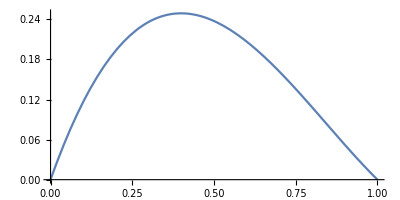

```mathematica
ss=solnCline[-0.147934503,0.7,0.7,ϵ];
Plot[y[p]/.ss,{p,0,1-ϵ},AspectRatio->0.5]
```

#### x0

```mathematica
x0::usage="x0[h_1,h_2,ϵ] stores the offset required to bring the centre (defined as p=1/2) to zero";
```

```mathematica
x0[h1_,h2_,ϵ_]:=x0[h1,h2,ϵ]=x[0.5]/.solnCline[speed[h1,h2],h1,h2,ϵ];
```